Numerical optimization for generalized finite difference stencils (involving multi-derivative terms).

Ansatz made:
δx^d_r∑_(m=-L_r)^R_r b_r∂_x^d_r f=∑_(i∈I) δx^d_i∑_(m_i=L_i)^R_i a_(i,m_i)∂_x^d_i [f]

Can construct:
- Explicit schemes
- Implicit, order matched
- Implicit, spectrally optimized, partial order matching
- Implicit, spectrally optimized, partial order matching, truncation error (at fixed order) tuned
- Explicit schemes with truncation error tuning for closures

Ref:
[1, arXiv:2302.14858] Spectrally-tuned compact finite-difference schemes with domain decomposition and applications to numerical relativity. Daszuta

```mathematica
(*acc/wp/pg*)
AG=25;PG=30;WP=60;IPOPTTOL=PG;
```

```mathematica
(*retain functions for plot dump*)
ωassoc=Association[];
```

```mathematica
(*retain stencils*)
Sassoc=Association[];
```

```mathematica
(*retain stencils as rules*)
Rassoc=Association[];
```

```mathematica
(*truncation error*)
Tassoc=Association[];
```

## [Init] Solvers

```mathematica
GFDSolver[eqs_,vars_,locWP_:WP]:=Module[{},
First@NSolve[
eqs,
vars,
WorkingPrecision->locWP
]
];
```

To use non-linear interior point at more stringent tolerances one can proceed as:

```mathematica
Needs["IPOPTLink`"];
ipoptopts=Options[IPOPTLink`Private`IPOPTSolve];
Options[IPOPTLink`Private`IPOPTSolve]={"acceptable_tol"->10^-(IPOPTTOL-5),"print_level"->1,"sb"->"yes"};
```

```mathematica
GFDSolverMin[eqs_,vars_,locPG_:PG,locAG_:AG,locWP_:WP,locMaxIt_:1000]:=Module[{},
FindMinimum[
eqs,vars,
WorkingPrecision->locWP,AccuracyGoal->locAG,PrecisionGoal->locPG,
Method->{Automatic,"Method"->"NonlinearInteriorPoint"},
MaxIterations->locMaxIt
]
];
```

```mathematica
(*If above has issues*)
GFDSolverMinFallback[eqs_,vars_,locPG_:PG,locAG_:AG,locWP_:WP,locMaxIt_:1000]:=Module[{},
NMinimize[
eqs,vars,WorkingPrecision->locWP,AccuracyGoal->locAG,PrecisionGoal->locPG
]
];
```

## [Init] Replacement rules (v1)

```mathematica
ruConjI={ⅈ->-ⅈ,-ⅈ->ⅈ};
ruTranspose={row->col,col->row};
ruContrImplode={A_[col]B_[row]:>B[A]};
```

## [Init] Definitions

```mathematica
vecM[M_]:=Table[{ix},{ix,-M,M}];
vecC[M_,η_]:=Table[{Cos[ix η]},{ix,-M,M}];
vecS[M_,η_]:=Table[{Sin[ix η]},{ix,-M,M}];
vecCS={Cv,Sv};
```

```mathematica
(*define error using derivative ansatz*)
errDefn[numTerms_]:=Sum[
((ⅈ η)^d[ix-1]Cv[row]av[ix-1][col]
+ⅈ (ⅈ η)^d[ix-1]Sv[row]av[ix-1][col]),
{ix,1,numTerms}]-((ⅈ η)^d[r]Cv[row]bv[col]+ⅈ(ⅈ η)^d[r]Sv[row]bv[col])
```

```mathematica
tarVec[numTerms_]:=Flatten@{Table[av[ix-1],{ix,1,numTerms}],bv};
```

```mathematica
(*build unweighted optimization functional - numTerms is RHS num*)
UWOptFunctional[numTerms_]:=UWOptFunctional[numTerms]=Module[{},
Expand[
(errDefn[numTerms]/.ruContrImplode)(errDefn[numTerms]/.ruConjI/.ruContrImplode)
]
];
```

```mathematica
(*build Q matrix diagonal elements*)QElementD[ixI_,numTerms_,fcnExp_]:=Module[{tarVars},
tarVars=tarVec[numTerms];
Cv[Cv]Coefficient[fcnExp,Cv[tarVars[[ixI]]]^2]
+Sv[Sv]Coefficient[fcnExp,Sv[tarVars[[ixI]]]^2]
]
(*build Q matrix off-diagonal elements*)
QElementOD[ixI_,ixJ_,numTerms_,fcnExp_]:=Module[
{tarVars,QIJcoeffs,QIJcoeffsRelevant},
tarVars=tarVec[numTerms];
QIJcoeffs={
Coefficient[fcnExp,Cv[tarVars[[ixI]]]],
Coefficient[fcnExp,Sv[tarVars[[ixI]]]]};

QIJcoeffsRelevant=Map[
Total[Cases[#,fac__ A_[tarVars[[ixJ]]]:>fac A[tarVars[[ixJ]]]]]&,
QIJcoeffs];

1/2 Total[
{QIJcoeffsRelevant[[1]]/.A_[tarVars[[ixJ]]]:>Cv[A],
QIJcoeffsRelevant[[2]]/.A_[tarVars[[ixJ]]]:>Sv[A]}
]
]
```

```mathematica
(*build Q matrix elements*)
QElement[ixI_,ixJ_,numTerms_]:=Module[{fcnExp},
fcnExp=UWOptFunctional[numTerms];

If[ixI==ixJ,
(*diagonal elements extract directly*)
QElementD[ixI,numTerms,fcnExp],
QElementOD[ixI,ixJ,numTerms,fcnExp]]
]
```

```mathematica
(*build full Q*)
Clear[Qmat];
Qmat[numTerms_]:=Qmat[numTerms]=Module[{},
Table[QElement[ixI,ixJ,numTerms],
{ixI,1,numTerms+1},{ixJ,1,numTerms+1}]
]

(*for integration*)
Clear[QreplaceElements];
QreplaceElements[w_]:=QreplaceElements[w]=Module[{Crow,Srow},
Crow=Transpose[vecC[w,η]];
Srow=Transpose[vecS[w,η]];

{
Cv[Cv]->Transpose[Crow].Crow,
Sv[Cv]->Transpose[Srow].Crow,
Cv[Sv]->Transpose[Crow].Srow,
Sv[Sv]->Transpose[Srow].Srow
}
];
```

```mathematica
(*Taylor expansion constraints*)
TEqnsTerms[dr_,d_,w_,numTeqns_]:=Module[
{maxd,dLHS,dRHS,TdresLHS,TdresRHS,Tdiff,TRHS,Teqns},
maxd=Max[{dr,Max[d]}];

dLHS=Total[Flatten[Table[δx^dr bv[dr,o] D[f[x], {x,dr}]/.x->x0+o δx,
{o,-w,w}]]];

dRHS=Total@Table[
Total[
Flatten[
Table[δx^d[[ixd]] av[d[[ixd]],o] D[f[x], {x,d[[ixd]]}]/.x->x0+o δx,
{o,-w,w}]
]
],
{ixd,1,Length[d]}
];

TdresLHS=Normal[Series[dLHS/.x0->0,{δx,0,numTeqns+2maxd+1}]];
TdresRHS=Normal[Series[dRHS/.x0->0,{δx,0,numTeqns+2maxd+1}]];
Tdiff=Expand[TdresLHS-TdresRHS];
TRHS=Table[Coefficient[Tdiff,Derivative[o][f][0]],{o,0,numTeqns-1}];
Teqns=Thread[TRHS==0]
];
```

```mathematica
(*given ranges {BL, A0L, ...}, {BR, A0R, ...} find abs-max*)
mAB2width[ML_,MR_]:=Module[{},
Max@Flatten[{Abs[ML],Abs[MR]}]
];
```

```mathematica
(*zero coefficient constraints*)
Clear[mZeroConstraints];
mZeroConstraints[dr_,d_,ML_,MR_]:=mZeroConstraints[dr,d,ML,MR]=Module[
{w,conb,cona},
w=mAB2width[ML,MR];
conb=Flatten@{
Table[bv[dr,ix]==0,{ix,-w,-ML[[1]]-1}],
Table[bv[dr,ix]==0,{ix,MR[[1]]+1,w}]};
cona=Table[
{
Table[av[d[[ixd]],ix]==0,{ix,-w,-ML[[1+ixd]]-1}],
Table[av[d[[ixd]],ix]==0,{ix,MR[[1+ixd]]+1,w}]},
{ixd,1,Length[d]}];
Flatten[{conb,cona}]
];
```

```mathematica
(*extract these vars..*)
mSolveVars[dr_,d_,ML_,MR_]:=Module[
{bvars,avars},
bvars=Table[bv[dr,ix],{ix,-ML[[1]],MR[[1]]}];
avars=Table[
Table[av[d[[ixd]],ix],{ix,-ML[[1+ixd]],MR[[1+ixd]]}],
{ixd,1,Length[d]}];
Flatten[{avars,bvars}]
];
```

```mathematica
mSolVec[dr_,d_,ML_,MR_]:=Module[
{w,dix,avec,bvec},
w=mAB2width[ML,MR];
avec=Table[
Table[av[d[[dix]],ix],{ix,-w,w}],
{dix,1,Length[d]}];
bvec=Table[bv[dr,ix],{ix,-w,w}];

Transpose@{Flatten@{avec,bvec}}
];
```

```mathematica
mRepDer[dr_,ds_]:=Module[{},
Flatten@{d[r]->dr,Table[d[ix-1]->ds[[ix]],{ix,1,Length[ds]}]}
];
```

```mathematica
(*modified wavenumber definition*)
Clear[GFDModWave];
GFDModWave[dr_,d_,ML_,MR_]:=Module[
{denom,numer,dix},

denom=Total[Table[
bv[dr,o]Exp[ⅈ ω o δx],
{o,-ML[[1]],MR[[1]]}]];

numer=0;

For[dix=1,dix≤Length[d],dix+=1,
numer=numer+δx^d[[dix]] Total[
Table[
(ⅈ ω)^d[[dix]] av[d[[dix]],o]Exp[ⅈ ω o δx],
{o,-ML[[dix+1]],MR[[dix+1]]}
]
];
];

(*remove scaling to get modified wave-number*)
(*sca numer/denom/.ω->η/δx*)

numer/denom/.ω->η/δx

(*denom=Total[Flatten[Table[Cb[o] Exp[ⅈ ω o δx],{o,-mBL,mBR}]]];
numer=Total[Flatten[Table[Ca[o] Exp[ⅈ ω o δx],{o,-mAL,mAR}]]];
modom=numer/denom/.Flatten[coeffs];ExpToTrig[modom]/.ω->η/δx*)
]
```

```mathematica
(*objective function for minimization*)
Clear[QObjectiveIntegrated];
QObjectiveIntegrated[γ_,dr_,ds_,ML_,MR_,WP_,AG_]:=QObjectiveIntegrated[γ,dr,ds,ML,MR,WP,AG]=Module[
{Γloc,zCons,UWQIntegrand,w,Qinteg,contrQinteg},

Γloc=ToExpression[γ];

zCons=mZeroConstraints[dr,ds,ML,MR];

w=mAB2width[ML,MR];

UWQIntegrand=ArrayFlatten[
Qmat[Length[ds]]/.QreplaceElements[w]
];

Qinteg=NIntegrate[Γloc[η](UWQIntegrand/.Flatten@Map[ToRules,zCons]/.mRepDer[dr,ds]),
{η,0,π},
WorkingPrecision->WP,AccuracyGoal->AG,PrecisionGoal->AG];

contrQinteg=(Transpose[Conjugate[mSolVec[dr,ds,ML,MR]]].Qinteg.mSolVec[dr,ds,ML,MR])[[1,1]];


Chop[
contrQinteg/.Flatten@Map[ToRules,zCons]
]
]
```

## [Init] Replacement rules (v2)

```mathematica
(*placeholder*)
```

## [Init] Convenience functions

```mathematica
ExportStencil[sol_,dr_,ds_,mL_,mR_,dp_]:=Module[
{M,ast,bst},
M=mAB2width[mL,mR];
bst=Chop@N[
Flatten@{
Table[0,{m,-M,-mL[[1]]-1}],
Table[bv[dr,m],{m,-mL[[1]],mR[[1]]}],
Table[0,{m,mR[[1]]+1,M}]
}/.sol,
dp];
ast=Chop@N[
Table[
Flatten@{
Table[0,{m,-M,-mL[[1+ix]]-1}],
Table[av[ds[[ix]],m],{m,-mL[[1+ix]],mR[[1+ix]]}],
Table[0,{m,mR[[1+ix]]+1,M}]
},{ix,1,Length[ds]}
]/.sol,dp];

{ast,bst}
];
```

```mathematica
(*for cut'n'paste*)
StencilProcessPython[tag_]:=Module[{str},
st=Sassoc[tag];
str="  '"<>tag<>"': _np.array(";
str=str<>StringReplace[
ToString[
{Flatten@Sassoc[tag][[1]],
Sassoc[tag][[2]]}
],{"{"->"[","}"->"]"}];
str=str<>"),"
];
```

```mathematica
(*requires a scheme to already be generated*)
TaylorRescaleRat[tag_,dr_,ds_,mL_,mR_,ord_]:=Module[
{coeffsbr,coeffsas,M,LHS,RHS,sLHS,sRHS,norm},
coeffsbr=Rationalize[Sassoc[tag],10^(-20)][[2]];
coeffsas=Rationalize[Sassoc[tag],10^(-20)][[1]];

M=mAB2width[mL,mR];

LHS=δx^dr (Table[
D[u[x],{x,dr}]/.x->x+ix δx,
{ix,-M,M}].coeffsbr);

RHS=Total@Table[
δx^ds[[ax]]coeffsas[[ax]].Table[
 D[u[x],{x,ds[[ax]]}]/.x->x+ix δx,
{ix,-M,M}],
{ax,1,Length[ds]}];

sLHS=Normal@Series[LHS,{δx,0,ord}];
sRHS=Normal@Series[RHS,{δx,0,ord}];

(*normalize with front-factor to have coefficient scale-agnostic*)
norm=Coefficient[sLHS,Derivative[dr][u][x]];

Expand[(sRHS-sLHS)/norm]
];
```

```mathematica
(*requires a scheme to already be generated*)
TaylorRescale[tag_,dr_,ds_,mL_,mR_,ord_]:=Module[
{coeffsbr,coeffsas,M,LHS,RHS,sLHS,sRHS,norm},
coeffsbr=Sassoc[tag][[2]];
coeffsas=Sassoc[tag][[1]];

M=mAB2width[mL,mR];

LHS=δx^dr (Table[
D[u[x],{x,dr}]/.x->x+ix δx,
{ix,-M,M}].coeffsbr);

RHS=Total@Table[
δx^ds[[ax]]coeffsas[[ax]].Table[
 D[u[x],{x,ds[[ax]]}]/.x->x+ix δx,
{ix,-M,M}],
{ax,1,Length[ds]}];

sLHS=Normal@Series[LHS,{δx,0,ord}];
sRHS=Normal@Series[RHS,{δx,0,ord}];

(*normalize with front-factor to have coefficient scale-agnostic*)
norm=Coefficient[sLHS,Derivative[dr][u][x]];

Chop@Expand[(sRHS-sLHS)/norm]
];
```

## [no η opt] Strict order matching approach (e.g. Pade,Hermite,imp. Hermite)

### [tag:"explicit[1,{0},{0,2},{0,2},O(4)]"] Explicit: dr=1, d={0}, mL={0,2}, mR={0,2}

```mathematica
(*Taylor constraints: wlog δx=1*)
dr=1;
ds={0};
mL={0,2};
mR={0,2};
(*one term (scaling) is fixed so -1*)
p=Total@Flatten[Table[Table[1,{i,-mL[[ixc]],mR[[ixc]]}],{ixc,1,Length[mL]}]]-1;
```

```mathematica
tCons=TEqnsTerms[dr,ds,mAB2width[mL,mR],p]/.δx->1;
zCons=mZeroConstraints[dr,ds,mL,mR];
```

```mathematica
(*fix overall scaling for b[d,0]*)
eqs=Flatten@{
tCons/.Flatten@Map[ToRules,zCons],
bv[dr,0]==1
};
```

```mathematica
vars=mSolveVars[dr,ds,mL,mR];
```

```mathematica
sols=GFDSolver[eqs,vars];
```

```mathematica
rsols=Rationalize[sols,10^(-20)];
```

```mathematica
ηMod=1/ⅈ^dr GFDModWave[dr,ds,mL,mR]/.rsols;
```

```mathematica
(*retain*)
tag="explicit[1,{0},{0,2},{0,2},O(4)]";
ωassoc[tag]=ηMod;
Sassoc[tag]=ExportStencil[sols,dr,ds,mL,mR,PG];
Tassoc[tag]=Normal@Series[1-1/η^dr ηMod,{η,0,2p+dr}];
```

```mathematica
-Tassoc[tag]
```

-η^4/30+η^6/252-η^8/4320+(17 η^10)/1995840

```mathematica
rsols/.(av[a__,b__]->c_):>(av[a,b]->12c)
```

{av[0,-2]→1,av[0,-1]→-8,av[0,0]→0,av[0,1]→8,av[0,2]→-1,bv[1,0]→1}

```mathematica
(* verify Taylor / zero constaints satisfied *)
tCons/.Flatten@Map[ToRules,zCons]/.Rationalize[sols,10^(-20)]
```

{True,True,True,True,True}

### [tag:"explicit[2,{0},{0,2},{0,2},O(4)]"] Explicit: dr=2, d={0}, mL={0,2}, mR={0,2}

```mathematica
(*Taylor constraints: wlog δx=1*)
dr=2;
ds={0};
mL={0,2};
mR={0,2};
(*one term (scaling) is fixed so -1*)
p=Total@Flatten[Table[Table[1,{i,-mL[[ixc]],mR[[ixc]]}],{ixc,1,Length[mL]}]]-1;
```

```mathematica
tCons=TEqnsTerms[dr,ds,mAB2width[mL,mR],p]/.δx->1;
zCons=mZeroConstraints[dr,ds,mL,mR];
```

```mathematica
(*fix overall scaling for b[d,0]*)
eqs=Flatten@{
tCons/.Flatten@Map[ToRules,zCons],
bv[dr,0]==1
};
```

```mathematica
vars=mSolveVars[dr,ds,mL,mR];
```

```mathematica
sols=GFDSolver[eqs,vars];
```

```mathematica
rsols=Rationalize[sols,10^(-20)];
```

```mathematica
ηMod=1/ⅈ^dr GFDModWave[dr,ds,mL,mR]/.rsols;
```

```mathematica
(*retain*)
tag="explicit[2,{0},{0,2},{0,2},O(4)]";
ωassoc[tag]=ηMod;
Sassoc[tag]=ExportStencil[sols,dr,ds,mL,mR,PG];
Tassoc[tag]=Normal@Series[1-1/η^dr ηMod,{η,0,2p+dr}];
Rassoc[tag]=rsols;
```

```mathematica
-Tassoc[tag]
```

-η^4/90+η^6/1008-η^8/21600+(17 η^10)/11975040-(31 η^12)/990662400

```mathematica
rsols/.(av[a__,b__]->c_):>(av[a,b]->12c)
```

{av[0,-2]→-1,av[0,-1]→16,av[0,0]→-30,av[0,1]→16,av[0,2]→-1,bv[2,0]→1}

```mathematica
(* verify Taylor / zero constaints satisfied *)
tCons/.Flatten@Map[ToRules,zCons]/.Rationalize[sols,10^(-20)]
```

{True,True,True,True,True}

### [tag:"explicit[1,{0},{0,3},{0,3},O(6)]"] Explicit: dr=1, d={0}, mL={0,3}, mR={0,3}

```mathematica
(*Taylor constraints: wlog δx=1*)
dr=1;
ds={0};
mL={0,3};
mR={0,3};
(*one term (scaling) is fixed so -1*)
p=Total@Flatten[Table[Table[1,{i,-mL[[ixc]],mR[[ixc]]}],{ixc,1,Length[mL]}]]-1;
```

```mathematica
tCons=TEqnsTerms[dr,ds,mAB2width[mL,mR],p]/.δx->1;
zCons=mZeroConstraints[dr,ds,mL,mR];
```

```mathematica
(*fix overall scaling for b[d,0]*)
eqs=Flatten@{
tCons/.Flatten@Map[ToRules,zCons],
bv[dr,0]==1
};
```

```mathematica
vars=mSolveVars[dr,ds,mL,mR];
```

```mathematica
sols=GFDSolver[eqs,vars];
```

```mathematica
rsols=Rationalize[sols,10^(-20)];
```

```mathematica
ηMod=1/ⅈ^dr GFDModWave[dr,ds,mL,mR]/.rsols;
```

```mathematica
(*retain*)
tag="explicit[1,{0},{0,3},{0,3},O(6)]";
ωassoc[tag]=ηMod;
Sassoc[tag]=ExportStencil[sols,dr,ds,mL,mR,PG];
Tassoc[tag]=Normal@Series[1-1/η^dr ηMod,{η,0,2p+dr}];
```

```mathematica
-Tassoc[tag]
```

-η^6/140+η^8/720-(7 η^10)/52800+η^12/122850-(13 η^14)/36288000

```mathematica
rsols/.(av[a__,b__]->c_):>(av[a,b]->60c)
```

{av[0,-3]→-1,av[0,-2]→9,av[0,-1]→-45,av[0,0]→0,av[0,1]→45,av[0,2]→-9,av[0,3]→1,bv[1,0]→1}

```mathematica
(* verify Taylor / zero constaints satisfied *)
tCons/.Flatten@Map[ToRules,zCons]/.Rationalize[sols,10^(-20)]
```

{True,True,True,True,True,True,True}

### [tag:"explicit[2,{0},{0,3},{0,3},O(6)]"] Explicit: dr=2, d={0}, mL={0,3}, mR={0,3}

```mathematica
(*Taylor constraints: wlog δx=1*)
dr=2;
ds={0};
mL={0,3};
mR={0,3};
(*one term (scaling) is fixed so -1*)
p=Total@Flatten[Table[Table[1,{i,-mL[[ixc]],mR[[ixc]]}],{ixc,1,Length[mL]}]]-1;
```

```mathematica
tCons=TEqnsTerms[dr,ds,mAB2width[mL,mR],p]/.δx->1;
zCons=mZeroConstraints[dr,ds,mL,mR];
```

```mathematica
(*fix overall scaling for b[d,0]*)
eqs=Flatten@{
tCons/.Flatten@Map[ToRules,zCons],
bv[dr,0]==1
};
```

```mathematica
vars=mSolveVars[dr,ds,mL,mR];
```

```mathematica
sols=GFDSolver[eqs,vars];
```

```mathematica
rsols=Rationalize[sols,10^(-20)];
```

```mathematica
ηMod=1/ⅈ^dr GFDModWave[dr,ds,mL,mR]/.rsols;
```

```mathematica
(*retain*)
tag="explicit[2,{0},{0,3},{0,3},O(6)]";
ωassoc[tag]=ηMod;
Sassoc[tag]=ExportStencil[sols,dr,ds,mL,mR,PG];
Tassoc[tag]=Normal@Series[1-1/η^dr ηMod,{η,0,2p+dr}];
Rassoc[tag]=rsols;
```

```mathematica
-Tassoc[tag]
```

-η^6/560+η^8/3600-(7 η^10)/316800+η^12/859950-(13 η^14)/290304000+(31 η^16)/23265792000

```mathematica
rsols/.(av[a__,b__]->c_):>(av[a,b]->2c)
```

{av[0,-3]→1/45,av[0,-2]→-3/10,av[0,-1]→3,av[0,0]→-49/9,av[0,1]→3,av[0,2]→-3/10,av[0,3]→1/45,bv[2,0]→1}

```mathematica
(* verify Taylor / zero constaints satisfied *)
tCons/.Flatten@Map[ToRules,zCons]/.Rationalize[sols,10^(-20)]
```

{True,True,True,True,True,True,True}

### [tag:"explicit[2,{0},{0,4},{0,4},O(8)]"] Explicit: dr=2, d={0}, mL={0,4}, mR={0,4}

```mathematica
(*Taylor constraints: wlog δx=1*)
dr=2;
ds={0};
mL={0,4};
mR={0,4};
(*one term (scaling) is fixed so -1*)
p=Total@Flatten[Table[Table[1,{i,-mL[[ixc]],mR[[ixc]]}],{ixc,1,Length[mL]}]]-1;
```

```mathematica
tCons=TEqnsTerms[dr,ds,mAB2width[mL,mR],p]/.δx->1;
zCons=mZeroConstraints[dr,ds,mL,mR];
```

```mathematica
(*fix overall scaling for b[d,0]*)
eqs=Flatten@{
tCons/.Flatten@Map[ToRules,zCons],
bv[dr,0]==1
};
```

```mathematica
vars=mSolveVars[dr,ds,mL,mR];
```

```mathematica
sols=GFDSolver[eqs,vars];
```

```mathematica
rsols=Rationalize[sols,10^(-20)];
```

```mathematica
ηMod=1/ⅈ^dr GFDModWave[dr,ds,mL,mR]/.rsols;
```

```mathematica
(*retain*)
tag="explicit[2,{0},{0,4},{0,4},O(8)]";
ωassoc[tag]=ηMod;
Sassoc[tag]=ExportStencil[sols,dr,ds,mL,mR,PG];
Tassoc[tag]=Normal@Series[1-1/η^dr ηMod,{η,0,2p+dr}];
Rassoc[tag]=rsols;
```

```mathematica
-Tassoc[tag]
```

-η^8/3150+η^10/13860-(19 η^12)/2293200+η^14/1587600-(457 η^16)/12954816000+(491 η^18)/318536064000-(164573 η^20)/3020727790080000

```mathematica
rsols/.(av[a__,b__]->c_):>(av[a,b]->10c)
```

{av[0,-4]→-1/56,av[0,-3]→16/63,av[0,-2]→-2,av[0,-1]→16,av[0,0]→-1025/36,av[0,1]→16,av[0,2]→-2,av[0,3]→16/63,av[0,4]→-1/56,bv[2,0]→1}

```mathematica
(* verify Taylor / zero constaints satisfied *)
tCons/.Flatten@Map[ToRules,zCons]/.Rationalize[sols,10^(-20)]
```

{True,True,True,True,True,True,True,True,True}

### [tag:"explicit[2,{0},{0,5},{0,5},O(10)]"] Explicit: dr=2, d={0}, mL={0,5}, mR={0,5}

```mathematica
(*Taylor constraints: wlog δx=1*)
dr=2;
ds={0};
mL={0,5};
mR={0,5};
(*one term (scaling) is fixed so -1*)
p=Total@Flatten[Table[Table[1,{i,-mL[[ixc]],mR[[ixc]]}],{ixc,1,Length[mL]}]]-1;
```

```mathematica
tCons=TEqnsTerms[dr,ds,mAB2width[mL,mR],p]/.δx->1;
zCons=mZeroConstraints[dr,ds,mL,mR];
```

```mathematica
(*fix overall scaling for b[d,0]*)
eqs=Flatten@{
tCons/.Flatten@Map[ToRules,zCons],
bv[dr,0]==1
};
```

```mathematica
vars=mSolveVars[dr,ds,mL,mR];
```

```mathematica
sols=GFDSolver[eqs,vars];
```

```mathematica
rsols=Rationalize[sols,10^(-20)];
```

```mathematica
ηMod=1/ⅈ^dr GFDModWave[dr,ds,mL,mR]/.rsols;
```

```mathematica
(*retain*)
tag="explicit[2,{0},{0,5},{0,5},O(10)]";
ωassoc[tag]=ηMod;
Sassoc[tag]=ExportStencil[sols,dr,ds,mL,mR,PG];
Tassoc[tag]=Normal@Series[1-1/η^dr ηMod,{η,0,2p+dr}];
Rassoc[tag]=rsols;
```

```mathematica
-Tassoc[tag]
```

-η^10/16632+(5 η^12)/275184-η^14/362880+(43 η^16)/155457792-(713 η^18)/34749388800+(317 η^20)/265558487040-(7141 η^22)/126321343948800+(1277 η^24)/571192163942400

```mathematica
rsols/.(av[a__,b__]->c_):>(av[a,b]->21c)
```

{av[0,-5]→1/150,av[0,-4]→-5/48,av[0,-3]→5/6,av[0,-2]→-5,av[0,-1]→35,av[0,0]→-36883/600,av[0,1]→35,av[0,2]→-5,av[0,3]→5/6,av[0,4]→-5/48,av[0,5]→1/150,bv[2,0]→1}

```mathematica
(* verify Taylor / zero constaints satisfied *)
tCons/.Flatten@Map[ToRules,zCons]/.Rationalize[sols,10^(-20)]
```

{True,True,True,True,True,True,True,True,True,True,True}

### [tag:"explicit[1,{0},{0,4},{0,4},O(8)]"] Explicit: dr=1, d={0}, mL={0,4}, mR={0,4}

```mathematica
(*Taylor constraints: wlog δx=1*)
dr=1;
ds={0};
mL={0,4};
mR={0,4};
(*one term (scaling) is fixed so -1*)
p=Total@Flatten[Table[Table[1,{i,-mL[[ixc]],mR[[ixc]]}],{ixc,1,Length[mL]}]]-1;
```

```mathematica
tCons=TEqnsTerms[dr,ds,mAB2width[mL,mR],p]/.δx->1;
zCons=mZeroConstraints[dr,ds,mL,mR];
```

```mathematica
(*fix overall scaling for b[d,0]*)
eqs=Flatten@{
tCons/.Flatten@Map[ToRules,zCons],
bv[dr,0]==1
};
```

```mathematica
vars=mSolveVars[dr,ds,mL,mR];
```

```mathematica
sols=GFDSolver[eqs,vars];
```

```mathematica
rsols=Rationalize[sols,10^(-20)];
```

```mathematica
ηMod=1/ⅈ^dr GFDModWave[dr,ds,mL,mR]/.rsols;
```

```mathematica
(*retain*)
tag="explicit[1,{0},{0,4},{0,4},O(8)]";
ωassoc[tag]=ηMod;
Sassoc[tag]=ExportStencil[sols,dr,ds,mL,mR,PG];
Tassoc[tag]=Normal@Series[1-1/η^dr ηMod,{η,0,2p+dr}];
```

```mathematica
-Tassoc[tag]
```

-η^8/630+η^10/2310-(19 η^12)/327600+η^14/198450-(457 η^16)/1439424000+(491 η^18)/31853606400

```mathematica
rsols/.(av[a__,b__]->c_):>(av[a,b]->c)
```

{av[0,-4]→-1/560,av[0,-3]→8/315,av[0,-2]→-1/5,av[0,-1]→8/5,av[0,0]→-205/72,av[0,1]→8/5,av[0,2]→-1/5,av[0,3]→8/315,av[0,4]→-1/560,bv[2,0]→1}

```mathematica
(* verify Taylor / zero constaints satisfied *)
tCons/.Flatten@Map[ToRules,zCons]/.Rationalize[sols,10^(-20)]
```

{True,True,True,True,True,True,True,True,True}

### [tag:"explicit[1,{0},{0,5},{0,5},O(10)]"] Explicit: dr=1, d={0}, mL={0,5}, mR={0,5}

```mathematica
(*Taylor constraints: wlog δx=1*)
dr=1;
ds={0};
mL={0,5};
mR={0,5};
(*one term (scaling) is fixed so -1*)
p=Total@Flatten[Table[Table[1,{i,-mL[[ixc]],mR[[ixc]]}],{ixc,1,Length[mL]}]]-1;
```

```mathematica
tCons=TEqnsTerms[dr,ds,mAB2width[mL,mR],p]/.δx->1;
zCons=mZeroConstraints[dr,ds,mL,mR];
```

```mathematica
(*fix overall scaling for b[d,0]*)
eqs=Flatten@{
tCons/.Flatten@Map[ToRules,zCons],
bv[dr,0]==1
};
```

```mathematica
vars=mSolveVars[dr,ds,mL,mR];
```

```mathematica
sols=GFDSolver[eqs,vars];
```

```mathematica
rsols=Rationalize[sols,10^(-20)];
```

```mathematica
ηMod=1/ⅈ^dr GFDModWave[dr,ds,mL,mR]/.rsols;
```

```mathematica
(*retain*)
tag="explicit[1,{0},{0,5},{0,5},O(10)]";
ωassoc[tag]=ηMod;
Sassoc[tag]=ExportStencil[sols,dr,ds,mL,mR,PG];
Tassoc[tag]=Normal@Series[1-1/η^dr ηMod,{η,0,2p+dr}];
```

```mathematica
-Tassoc[tag]
```

-η^10/2772+(5 η^12)/39312-η^14/45360+(43 η^16)/17273088-(713 η^18)/3474938880+(317 η^20)/24141680640-(7141 η^22)/10526778662400

```mathematica
rsols/.(av[a__,b__]->c_):>(av[a,b]->21c)
```

{av[0,-5]→-1/60,av[0,-4]→5/24,av[0,-3]→-5/4,av[0,-2]→5,av[0,-1]→-35/2,av[0,0]→0,av[0,1]→35/2,av[0,2]→-5,av[0,3]→5/4,av[0,4]→-5/24,av[0,5]→1/60,bv[1,0]→1}

```mathematica
(* verify Taylor / zero constaints satisfied *)
tCons/.Flatten@Map[ToRules,zCons]/.Rationalize[sols,10^(-20)]
```

{True,True,True,True,True,True,True,True,True,True,True}

### [tag:"explicit[1,{0},{0,2},{0,4},O(6)]"] Explicit: dr=1, d={0}, mL={0,2}, mR={0,4}

```mathematica
(*Taylor constraints: wlog δx=1*)
dr=1;
ds={0};
mL={0,2};
mR={0,4};
(*one term (scaling) is fixed so -1*)
p=Total@Flatten[Table[Table[1,{i,-mL[[ixc]],mR[[ixc]]}],{ixc,1,Length[mL]}]]-1;
```

```mathematica
tCons=TEqnsTerms[dr,ds,mAB2width[mL,mR],p]/.δx->1;
zCons=mZeroConstraints[dr,ds,mL,mR];
```

```mathematica
(*fix overall scaling for b[d,0]*)
eqs=Flatten@{
tCons/.Flatten@Map[ToRules,zCons],
bv[dr,0]==1
};
```

```mathematica
vars=mSolveVars[dr,ds,mL,mR];
```

```mathematica
sols=GFDSolver[eqs,vars];
```

```mathematica
rsols=Rationalize[sols,10^(-20)];
```

```mathematica
ηMod=1/ⅈ^dr GFDModWave[dr,ds,mL,mR]/.rsols;
```

```mathematica
(*retain*)
tag="explicit[1,{0},{0,2},{0,4},O(6)]";
ωassoc[tag]=ηMod;
Sassoc[tag]=ExportStencil[sols,dr,ds,mL,mR,PG];
Tassoc[tag]=Normal@Series[1-1/η^dr ηMod,{η,0,2p+dr}];
```

```mathematica
-Tassoc[tag]
```

η^6/105+(ⅈ η^7)/120-η^8/180-(ⅈ η^9)/360+(47 η^10)/39600+(19 ⅈ η^11)/43200-(431 η^12)/2948400-(ⅈ η^13)/22680+(37 η^14)/3024000+(457 ⅈ η^15)/145152000

```mathematica
rsols/.(av[a__,b__]->c_):>(av[a,b]->60c)
```

{av[0,-2]→2,av[0,-1]→-24,av[0,0]→-35,av[0,1]→80,av[0,2]→-30,av[0,3]→8,av[0,4]→-1,bv[1,0]→1}

```mathematica
(* verify Taylor / zero constaints satisfied *)
tCons/.Flatten@Map[ToRules,zCons]/.Rationalize[sols,10^(-20)]
```

{True,True,True,True,True,True,True}

### [tag:"explicit[1,{0},{0,3},{0,1},O(4)]"] Explicit: dr=1, d={0}, mL={0,3}, mR={0,1}

```mathematica
(*Taylor constraints: wlog δx=1*)
dr=1;
ds={0};
mL={0,3};
mR={0,1};
(*one term (scaling) is fixed so -1*)
p=Total@Flatten[Table[Table[1,{i,-mL[[ixc]],mR[[ixc]]}],{ixc,1,Length[mL]}]]-1;
```

```mathematica
tCons=TEqnsTerms[dr,ds,mAB2width[mL,mR],p]/.δx->1;
zCons=mZeroConstraints[dr,ds,mL,mR];
```

```mathematica
(*fix overall scaling for b[d,0]*)
eqs=Flatten@{
tCons/.Flatten@Map[ToRules,zCons],
bv[dr,0]==1
};
```

```mathematica
vars=mSolveVars[dr,ds,mL,mR];
```

```mathematica
sols=GFDSolver[eqs,vars];
```

```mathematica
rsols=Rationalize[sols,10^(-20)];
```

```mathematica
ηMod=1/ⅈ^dr GFDModWave[dr,ds,mL,mR]/.rsols;
```

```mathematica
(*retain*)
tag="explicit[1,{0},{0,3},{0,1},O(4)]";
ωassoc[tag]=ηMod;
Sassoc[tag]=ExportStencil[sols,dr,ds,mL,mR,PG];
Tassoc[tag]=Normal@Series[1-1/η^dr ηMod,{η,0,2p+dr}];
```

```mathematica
-Tassoc[tag]
```

η^4/20-(ⅈ η^5)/24-η^6/42+(ⅈ η^7)/96+(11 η^8)/2880-(7 ⅈ η^9)/5760-(229 η^10)/665280+(ⅈ η^11)/11340

```mathematica
rsols/.(av[a__,b__]->c_):>(av[a,b]->12c)
```

{av[0,-3]→-1,av[0,-2]→6,av[0,-1]→-18,av[0,0]→10,av[0,1]→3,bv[1,0]→1}

```mathematica
(* verify Taylor / zero constaints satisfied *)
tCons/.Flatten@Map[ToRules,zCons]/.Rationalize[sols,10^(-20)]
```

{True,True,True,True,True}

### [tag:"explicit[1,{0},{0,4},{0,2},O(6)]"] Explicit: dr=1, d={0}, mL={0,4}, mR={0,2}

```mathematica
(*Taylor constraints: wlog δx=1*)
dr=1;
ds={0};
mL={0,4};
mR={0,2};
(*one term (scaling) is fixed so -1*)
p=Total@Flatten[Table[Table[1,{i,-mL[[ixc]],mR[[ixc]]}],{ixc,1,Length[mL]}]]-1;
```

```mathematica
tCons=TEqnsTerms[dr,ds,mAB2width[mL,mR],p]/.δx->1;
zCons=mZeroConstraints[dr,ds,mL,mR];
```

```mathematica
(*fix overall scaling for b[d,0]*)
eqs=Flatten@{
tCons/.Flatten@Map[ToRules,zCons],
bv[dr,0]==1
};
```

```mathematica
vars=mSolveVars[dr,ds,mL,mR];
```

```mathematica
sols=GFDSolver[eqs,vars];
```

```mathematica
rsols=Rationalize[sols,10^(-20)];
```

```mathematica
ηMod=1/ⅈ^dr GFDModWave[dr,ds,mL,mR]/.rsols;
```

```mathematica
(*retain*)
tag="explicit[1,{0},{0,4},{0,2},O(6)]";
ωassoc[tag]=ηMod;
Sassoc[tag]=ExportStencil[sols,dr,ds,mL,mR,PG];
Tassoc[tag]=Normal@Series[1-1/η^dr ηMod,{η,0,2p+dr}];
```

```mathematica
-Tassoc[tag]
```

η^6/105-(ⅈ η^7)/120-η^8/180+(ⅈ η^9)/360+(47 η^10)/39600-(19 ⅈ η^11)/43200-(431 η^12)/2948400+(ⅈ η^13)/22680+(37 η^14)/3024000-(457 ⅈ η^15)/145152000

```mathematica
rsols/.(av[a__,b__]->c_):>(av[a,b]->60c)
```

{av[0,-4]→1,av[0,-3]→-8,av[0,-2]→30,av[0,-1]→-80,av[0,0]→35,av[0,1]→24,av[0,2]→-2,bv[1,0]→1}

```mathematica
(* verify Taylor / zero constaints satisfied *)
tCons/.Flatten@Map[ToRules,zCons]/.Rationalize[sols,10^(-20)]
```

{True,True,True,True,True,True,True}

### [tag:"explicit[1,{0},{0,5},{0,3},O(8)]"] Explicit: dr=1, d={0}, mL={0,5}, mR={0,3}

```mathematica
(*Taylor constraints: wlog δx=1*)
dr=1;
ds={0};
mL={0,5};
mR={0,3};
(*one term (scaling) is fixed so -1*)
p=Total@Flatten[Table[Table[1,{i,-mL[[ixc]],mR[[ixc]]}],{ixc,1,Length[mL]}]]-1;
```

```mathematica
tCons=TEqnsTerms[dr,ds,mAB2width[mL,mR],p]/.δx->1;
zCons=mZeroConstraints[dr,ds,mL,mR];
```

```mathematica
(*fix overall scaling for b[d,0]*)
eqs=Flatten@{
tCons/.Flatten@Map[ToRules,zCons],
bv[dr,0]==1
};
```

```mathematica
vars=mSolveVars[dr,ds,mL,mR];
```

```mathematica
sols=GFDSolver[eqs,vars];
```

```mathematica
rsols=Rationalize[sols,10^(-20)];
```

```mathematica
ηMod=1/ⅈ^dr GFDModWave[dr,ds,mL,mR]/.rsols;
```

```mathematica
(*retain*)
tag="explicit[1,{0},{0,5},{0,3},O(8)]";
ωassoc[tag]=ηMod;
Sassoc[tag]=ExportStencil[sols,dr,ds,mL,mR,PG];
Tassoc[tag]=Normal@Series[1-1/η^dr ηMod,{η,0,2p+dr}];
```

```mathematica
-Tassoc[tag]
```

η^8/504-(ⅈ η^9)/560-(5 η^10)/3696+(ⅈ η^11)/1344+(47 η^12)/131040-(ⅈ η^13)/6720-(71 η^14)/1270080+(43 ⅈ η^15)/2257920+(6907 η^16)/1151539200-(713 ⅈ η^17)/406425600-(24511 η^18)/50965770240+(317 ⅈ η^19)/2554675200

```mathematica
rsols/.(av[a__,b__]->c_):>(av[a,b]->12c)
```

{av[0,-5]→-3/70,av[0,-4]→3/7,av[0,-3]→-2,av[0,-2]→6,av[0,-1]→-15,av[0,0]→27/5,av[0,1]→6,av[0,2]→-6/7,av[0,3]→1/14,bv[1,0]→1}

```mathematica
(* verify Taylor / zero constaints satisfied *)
tCons/.Flatten@Map[ToRules,zCons]/.Rationalize[sols,10^(-20)]
```

{True,True,True,True,True,True,True,True,True}

### [tag:"explicit[1,{0},{0,6},{0,4},O(10)]"] Explicit: dr=1, d={0}, mL={0,6}, mR={0,4}

```mathematica
(*Taylor constraints: wlog δx=1*)
dr=1;
ds={0};
mL={0,6};
mR={0,4};
(*one term (scaling) is fixed so -1*)
p=Total@Flatten[Table[Table[1,{i,-mL[[ixc]],mR[[ixc]]}],{ixc,1,Length[mL]}]]-1;
```

```mathematica
tCons=TEqnsTerms[dr,ds,mAB2width[mL,mR],p]/.δx->1;
zCons=mZeroConstraints[dr,ds,mL,mR];
```

```mathematica
(*fix overall scaling for b[d,0]*)
eqs=Flatten@{
tCons/.Flatten@Map[ToRules,zCons],
bv[dr,0]==1
};
```

```mathematica
vars=mSolveVars[dr,ds,mL,mR];
```

```mathematica
sols=GFDSolver[eqs,vars];
```

```mathematica
rsols=Rationalize[sols,10^(-20)];
```

```mathematica
ηMod=1/ⅈ^dr GFDModWave[dr,ds,mL,mR]/.rsols;
```

```mathematica
(*retain*)
tag="explicit[1,{0},{0,6},{0,4},O(10)]";
ωassoc[tag]=ηMod;
Sassoc[tag]=ExportStencil[sols,dr,ds,mL,mR,PG];
Tassoc[tag]=Normal@Series[1-1/η^dr ηMod,{η,0,2p+dr}];
```

```mathematica
-Tassoc[tag]
```

η^10/2310-(ⅈ η^11)/2520-(11 η^12)/32760+(ⅈ η^13)/5040+η^14/9450-(29 ⅈ η^15)/604800-(1433 η^16)/71971200+(569 ⅈ η^17)/76204800+(7541 η^18)/2895782400-(367 ⅈ η^19)/435456000-(25807 η^20)/100590336000+(14797 ⅈ η^21)/201180672000+(8507 η^22)/425324390400-(37859 ⅈ η^23)/7322976460800

```mathematica
rsols/.(av[a__,b__]->c_):>(av[a,b]->21c)
```

{av[0,-6]→1/60,av[0,-5]→-1/5,av[0,-4]→9/8,av[0,-3]→-4,av[0,-2]→21/2,av[0,-1]→-126/5,av[0,0]→77/10,av[0,1]→12,av[0,2]→-9/4,av[0,3]→1/3,av[0,4]→-1/40,bv[1,0]→1}

```mathematica
(* verify Taylor / zero constaints satisfied *)
tCons/.Flatten@Map[ToRules,zCons]/.Rationalize[sols,10^(-20)]
```

{True,True,True,True,True,True,True,True,True,True,True}

### [tag:"pade[1,{0},{1,1},{1,1},O(4)]"] Pade: dr=1, d={0}, mL={1,1}, mR={1,1}

```mathematica
(*Taylor constraints: wlog δx=1*)
dr=1;
ds={0};
mL={1,1};
mR={1,1};
(*one term (scaling) is fixed so -1*)
p=Total@Flatten[Table[Table[1,{i,-mL[[ixc]],mR[[ixc]]}],{ixc,1,Length[mL]}]]-1;
```

```mathematica
tCons=TEqnsTerms[dr,ds,mAB2width[mL,mR],p]/.δx->1;
zCons=mZeroConstraints[dr,ds,mL,mR];
```

```mathematica
(*fix overall scaling for b[d,0]*)
eqs=Flatten@{
tCons/.Flatten@Map[ToRules,zCons],
bv[dr,0]==1
};
```

```mathematica
vars=mSolveVars[dr,ds,mL,mR];
```

```mathematica
sols=GFDSolver[eqs,vars];
```

```mathematica
rsols=Rationalize[sols,10^(-20)];
```

```mathematica
ηMod=1/ⅈ^dr GFDModWave[dr,ds,mL,mR]/.rsols;
```

```mathematica
(*retain*)
tag="pade[1,{0},{1,1},{1,1},O(4)]";
ωassoc[tag]=ηMod;
Sassoc[tag]=ExportStencil[sols,dr,ds,mL,mR,PG];
Tassoc[tag]=Normal@Series[1-1/η^dr ηMod,{η,0,2p+dr}];
```

```mathematica
TaylorRescaleRat[tag,dr,ds,mL,mR,12]
```

-1/180 δx^4 u^(5)[x]-(δx^6 u^(7)[x])/3780-(δx^8 u^(9)[x])/181440-(δx^10 u^(11)[x])/14968800

```mathematica
-Tassoc[tag]
```

-η^4/180-η^6/1512-η^8/25920+η^10/3991680

```mathematica
rsols/.(av[a__,b__]->c_):>(4av[a,b]->4c)
```

{4 av[0,-1]→-3,4 av[0,0]→0,4 av[0,1]→3,bv[1,-1]→1/4,bv[1,0]→1,bv[1,1]→1/4}

### [tag:"pade[1,{0},{1,2},{1,2},O(6)]"] Pade: dr=1, d={0}, mL={1,2}, mR={1,2}

```mathematica
(*Taylor constraints: wlog δx=1*)
dr=1;
ds={0};
mL={1,2};
mR={1,2};
(*one term (scaling) is fixed so -1*)
p=Total@Flatten[Table[Table[1,{i,-mL[[ixc]],mR[[ixc]]}],{ixc,1,Length[mL]}]]-1;
```

```mathematica
tCons=TEqnsTerms[dr,ds,mAB2width[mL,mR],p]/.δx->1;
zCons=mZeroConstraints[dr,ds,mL,mR];
```

```mathematica
(*fix overall scaling for b[d,0]*)
eqs=Flatten@{
tCons/.Flatten@Map[ToRules,zCons],
bv[dr,0]==1
};
```

```mathematica
vars=mSolveVars[dr,ds,mL,mR];
```

```mathematica
sols=GFDSolver[eqs,vars];
```

```mathematica
rsols=Rationalize[sols,10^(-20)];
```

```mathematica
ηMod=1/ⅈ^dr GFDModWave[dr,ds,mL,mR]/.rsols;
```

```mathematica
(*retain*)
tag="pade[1,{0},{1,2},{1,2},O(6)]";
ωassoc[tag]=ηMod;
Sassoc[tag]=ExportStencil[sols,dr,ds,mL,mR,PG];
Tassoc[tag]=Normal@Series[1-1/η^dr ηMod,{η,0,2p+dr}];
```

```mathematica
-Tassoc[tag]
```

-η^6/2100-η^8/18000-(19 η^10)/3960000-(47 η^12)/184275000+η^14/504000000

```mathematica
rsols/.(av[a__,b__]->c_):>(av[a,b]->36c)
```

{av[0,-2]→-1,av[0,-1]→-28,av[0,0]→0,av[0,1]→28,av[0,2]→1,bv[1,-1]→1/3,bv[1,0]→1,bv[1,1]→1/3}

### [tag:"pade[1,{0},{1,3},{1,3},O(8)]"] Pade: dr=1, d={0}, mL={1,3}, mR={1,3}

```mathematica
(*Taylor constraints: wlog δx=1*)
dr=1;
ds={0};
mL={1,3};
mR={1,3};
(*one term (scaling) is fixed so -1*)
p=Total@Flatten[Table[Table[1,{i,-mL[[ixc]],mR[[ixc]]}],{ixc,1,Length[mL]}]]-1;
```

```mathematica
tCons=TEqnsTerms[dr,ds,mAB2width[mL,mR],p]/.δx->1;
zCons=mZeroConstraints[dr,ds,mL,mR];
```

```mathematica
(*fix overall scaling for b[d,0]*)
eqs=Flatten@{
tCons/.Flatten@Map[ToRules,zCons],
bv[dr,0]==1
};
```

```mathematica
vars=mSolveVars[dr,ds,mL,mR];
```

```mathematica
sols=GFDSolver[eqs,vars];
```

```mathematica
rsols=Rationalize[sols,10^(-20)];
```

```mathematica
ηMod=1/ⅈ^dr GFDModWave[dr,ds,mL,mR]/.rsols;
```

```mathematica
(*retain*)
tag="pade[1,{0},{1,3},{1,3},O(8)]";
ωassoc[tag]=ηMod;
Sassoc[tag]=ExportStencil[sols,dr,ds,mL,mR,PG];
Tassoc[tag]=Normal@Series[1-1/η^dr ηMod,{η,0,2p+dr}];
```

```mathematica
-Tassoc[tag]
```

-η^8/17640-η^10/226380-(211 η^12)/449467200-(67 η^14)/2178187200-(14911 η^16)/13824228096000+(27163 η^18)/267681781382400

```mathematica
rsols/.(av[a__,b__]->c_):>(av[a,b]->480c)
```

{av[0,-3]→1,av[0,-2]→-24,av[0,-1]→-375,av[0,0]→0,av[0,1]→375,av[0,2]→24,av[0,3]→-1,bv[1,-1]→3/8,bv[1,0]→1,bv[1,1]→3/8}

### [tag:"pade[1,{0},{2,1},{2,1},O(6)]"] Pade: dr=1, d={0}, mL={2,1}, mR={2,1}

```mathematica
(*Taylor constraints: wlog δx=1*)
dr=1;
ds={0};
mL={2,1};
mR={2,1};
(*one term (scaling) is fixed so -1*)
p=Total@Flatten[Table[Table[1,{i,-mL[[ixc]],mR[[ixc]]}],{ixc,1,Length[mL]}]]-1;
```

```mathematica
tCons=TEqnsTerms[dr,ds,mAB2width[mL,mR],p]/.δx->1;
zCons=mZeroConstraints[dr,ds,mL,mR];
```

```mathematica
(*fix overall scaling for b[d,0]*)
eqs=Flatten@{
tCons/.Flatten@Map[ToRules,zCons],
bv[dr,0]==1
};
```

```mathematica
vars=mSolveVars[dr,ds,mL,mR];
```

```mathematica
sols=GFDSolver[eqs,vars];
```

```mathematica
ηMod=1/ⅈ^dr GFDModWave[dr,ds,mL,mR]/.sols;
```

```mathematica
(*retain*)
tag="pade[1,{0},{2,1},{2,1},O(6)]";
ωassoc[tag]=ηMod;
Sassoc[tag]=ExportStencil[sols,dr,ds,mL,mR,PG];
Tassoc[tag]=N[Chop@Series[1-1/η^dr ηMod,{η,0,2p+dr}],4];
```

### [tag:"pade[1,{0},{2,2},{2,2},O(8)]"] Pade: dr=1, d={0}, mL={2,2}, mR={2,2}

```mathematica
(*Taylor constraints: wlog δx=1*)
dr=1;
ds={0};
mL={2,2};
mR={2,2};
(*one term (scaling) is fixed so -1*)
p=Total@Flatten[Table[Table[1,{i,-mL[[ixc]],mR[[ixc]]}],{ixc,1,Length[mL]}]]-1;
```

```mathematica
tCons=TEqnsTerms[dr,ds,mAB2width[mL,mR],p]/.δx->1;
zCons=mZeroConstraints[dr,ds,mL,mR];
```

```mathematica
(*fix overall scaling for b[d,0]*)
eqs=Flatten@{
tCons/.Flatten@Map[ToRules,zCons],
bv[dr,0]==1
};
```

```mathematica
vars=mSolveVars[dr,ds,mL,mR];
```

```mathematica
sols=GFDSolver[eqs,vars];
```

```mathematica
ηMod=1/ⅈ^dr GFDModWave[dr,ds,mL,mR]/.sols;
```

```mathematica
(*retain*)
tag="pade[1,{0},{2,2},{2,2},O(8)]";
ωassoc[tag]=ηMod;
Sassoc[tag]=ExportStencil[sols,dr,ds,mL,mR,PG];
Tassoc[tag]=N[Chop@Series[1-1/η^dr ηMod,{η,0,2p+dr}],4];
```

### [tag:"pade[2,{0},{1,1},{1, 1},O(4)]"] Pade: dr=2, d={0}, mL={1,1}, mR={1,1}

```mathematica
(*Taylor constraints: wlog δx=1*)
dr=2;
ds={0};
mL={1,1};
mR={1,1};
(*one term (scaling) is fixed so -1*)
p=Total@Flatten[Table[Table[1,{i,-mL[[ixc]],mR[[ixc]]}],{ixc,1,Length[mL]}]]-1;
```

```mathematica
tCons=TEqnsTerms[dr,ds,mAB2width[mL,mR],p]/.δx->1;
zCons=mZeroConstraints[dr,ds,mL,mR];
```

```mathematica
(*fix overall scaling for b[d,0]*)
eqs=Flatten@{
tCons/.Flatten@Map[ToRules,zCons],
bv[dr,0]==1
};
```

```mathematica
vars=mSolveVars[dr,ds,mL,mR];
```

```mathematica
sols=GFDSolver[eqs,vars];
```

```mathematica
rsols=Rationalize[sols,10^(-20)];
```

```mathematica
ηMod=1/ⅈ^dr GFDModWave[dr,ds,mL,mR]/.rsols;
```

```mathematica
(*retain*)
tag="pade[2,{0},{1,1},{1,1},O(4)]";
ωassoc[tag]=ηMod;
Sassoc[tag]=ExportStencil[sols,dr,ds,mL,mR,PG];
Tassoc[tag]=Normal@Series[1-1/η^dr ηMod,{η,0,2p+dr}];
Rassoc[tag]=rsols;
```

```mathematica
-Tassoc[tag]
```

-η^4/240-η^6/6048+η^8/86400+(19 η^10)/15966720-(41 η^12)/15850598400

```mathematica
rsols/.(av[a__,b__]->c_):>(av[a,b]->5c)
```

{av[0,-1]→6,av[0,0]→-12,av[0,1]→6,bv[2,-1]→1/10,bv[2,0]→1,bv[2,1]→1/10}

```mathematica
(* verify Taylor / zero constaints satisfied *)
tCons/.Flatten@Map[ToRules,zCons]/.Rationalize[sols,10^(-20)]
```

{True,True,True,True,True}

### [tag:"pade[2,{0},{1,2},{1,2},O(6)]"] Pade: dr=2, d={0}, mL={1,2}, mR={1,2}

```mathematica
(*Taylor constraints: wlog δx=1*)
dr=2;
ds={0};
mL={1,2};
mR={1,2};
(*one term (scaling) is fixed so -1*)
p=Total@Flatten[Table[Table[1,{i,-mL[[ixc]],mR[[ixc]]}],{ixc,1,Length[mL]}]]-1;
```

```mathematica
tCons=TEqnsTerms[dr,ds,mAB2width[mL,mR],p]/.δx->1;
zCons=mZeroConstraints[dr,ds,mL,mR];
```

```mathematica
(*fix overall scaling for b[d,0]*)
eqs=Flatten@{
tCons/.Flatten@Map[ToRules,zCons],
bv[dr,0]==1
};
```

```mathematica
vars=mSolveVars[dr,ds,mL,mR];
```

```mathematica
sols=GFDSolver[eqs,vars];
```

```mathematica
rsols=Rationalize[sols,10^(-20)];
```

```mathematica
ηMod=1/ⅈ^dr GFDModWave[dr,ds,mL,mR]/.rsols;
```

```mathematica
(*retain*)
tag="pade[2,{0},{1,2},{1,2},O(6)]";
ωassoc[tag]=ηMod;
Sassoc[tag]=ExportStencil[sols,dr,ds,mL,mR,PG];
Tassoc[tag]=Normal@Series[1-1/η^dr ηMod,{η,0,2p+dr}];
Rassoc[tag]=rsols;
```

```mathematica
-Tassoc[tag]
```

-(23 η^6)/75600-η^8/54000+η^10/7920000+(62 η^12)/483721875+(3439 η^14)/326592000000+(39947 η^16)/305363520000000

```mathematica
rsols/.(av[a__,b__]->c_):>(av[a,b]->44c)
```

{av[0,-2]→3,av[0,-1]→48,av[0,0]→-102,av[0,1]→48,av[0,2]→3,bv[2,-1]→2/11,bv[2,0]→1,bv[2,1]→2/11}

```mathematica
(* verify Taylor / zero constaints satisfied *)
tCons/.Flatten@Map[ToRules,zCons]/.Rationalize[sols,10^(-20)]
```

{True,True,True,True,True,True,True}

### [tag:"pade[2,{0},{1,3},{1,3},O(8)]"] Pade: dr=2, d={0}, mL={1,3}, mR={1,3}

```mathematica
(*Taylor constraints: wlog δx=1*)
dr=2;
ds={0};
mL={1,3};
mR={1,3};
(*one term (scaling) is fixed so -1*)
p=Total@Flatten[Table[Table[1,{i,-mL[[ixc]],mR[[ixc]]}],{ixc,1,Length[mL]}]]-1;
```

```mathematica
tCons=TEqnsTerms[dr,ds,mAB2width[mL,mR],p]/.δx->1;
zCons=mZeroConstraints[dr,ds,mL,mR];
```

```mathematica
(*fix overall scaling for b[d,0]*)
eqs=Flatten@{
tCons/.Flatten@Map[ToRules,zCons],
bv[dr,0]==1
};
```

```mathematica
vars=mSolveVars[dr,ds,mL,mR];
```

```mathematica
sols=GFDSolver[eqs,vars];
```

```mathematica
rsols=Rationalize[sols,10^(-20)];
```

```mathematica
ηMod=1/ⅈ^dr GFDModWave[dr,ds,mL,mR]/.rsols;
```

```mathematica
(*retain*)
tag="pade[2,{0},{1,3},{1,3},O(8)]";
ωassoc[tag]=ηMod;
Sassoc[tag]=ExportStencil[sols,dr,ds,mL,mR,PG];
Tassoc[tag]=Normal@Series[1-1/η^dr ηMod,{η,0,2p+dr}];
```

```mathematica
-Tassoc[tag]
```

-(43 η^8)/1411200-(227 η^10)/173859840-(1067 η^12)/57531801600+(21691 η^14)/2230463692800+(38305367 η^16)/31851021533184000+(1511521229 η^18)/21928491530846208000-(316693673137 η^20)/415902695160828395520000

```mathematica
rsols/.(av[a__,b__]->c_):>(av[a,b]->152c)
```

{av[0,-3]→-23/45,av[0,-2]→102/5,av[0,-1]→147,av[0,0]→-3004/9,av[0,1]→147,av[0,2]→102/5,av[0,3]→-23/45,bv[2,-1]→9/38,bv[2,0]→1,bv[2,1]→9/38}

```mathematica
(* verify Taylor / zero constaints satisfied *)
tCons/.Flatten@Map[ToRules,zCons]/.Rationalize[sols,10^(-20)]
```

{True,True,True,True,True,True,True,True,True}

### [tag:"pade[2,{0},{2,2},{2,2},O(8)]"] Pade: dr=2, d={0}, mL={2,2}, mR={2,2}

```mathematica
(*Taylor constraints: wlog δx=1*)
dr=2;
ds={0};
mL={2,2};
mR={2,2};
(*one term (scaling) is fixed so -1*)
p=Total@Flatten[Table[Table[1,{i,-mL[[ixc]],mR[[ixc]]}],{ixc,1,Length[mL]}]]-1;
```

```mathematica
tCons=TEqnsTerms[dr,ds,mAB2width[mL,mR],p]/.δx->1;
zCons=mZeroConstraints[dr,ds,mL,mR];
```

```mathematica
(*fix overall scaling for b[d,0]*)
eqs=Flatten@{
tCons/.Flatten@Map[ToRules,zCons],
bv[dr,0]==1
};
```

```mathematica
vars=mSolveVars[dr,ds,mL,mR];
```

```mathematica
sols=GFDSolver[eqs,vars];
```

```mathematica
ηMod=1/ⅈ^dr GFDModWave[dr,ds,mL,mR]/.sols;
```

```mathematica
(*retain*)
tag="pade[2,{0},{2,2},{2,2},O(8)]";
ωassoc[tag]=ηMod;
Sassoc[tag]=ExportStencil[sols,dr,ds,mL,mR,PG];
Tassoc[tag]=N[Chop@Series[1-1/η^dr ηMod,{η,0,2p+dr}],4];
```

### [tag:"pade[2,{0},{2,3},{2,3},O(10)]"] Pade: dr=2, d={0}, mL={2,3}, mR={2,3}

```mathematica
(*Taylor constraints: wlog δx=1*)
dr=2;
ds={0};
mL={2,3};
mR={2,3};
(*one term (scaling) is fixed so -1*)
p=Total@Flatten[Table[Table[1,{i,-mL[[ixc]],mR[[ixc]]}],{ixc,1,Length[mL]}]]-1;
```

```mathematica
tCons=TEqnsTerms[dr,ds,mAB2width[mL,mR],p]/.δx->1;
zCons=mZeroConstraints[dr,ds,mL,mR];
```

```mathematica
(*fix overall scaling for b[d,0]*)
eqs=Flatten@{
tCons/.Flatten@Map[ToRules,zCons],
bv[dr,0]==1
};
```

```mathematica
vars=mSolveVars[dr,ds,mL,mR];
```

```mathematica
sols=GFDSolver[eqs,vars];
```

```mathematica
ηMod=1/ⅈ^dr GFDModWave[dr,ds,mL,mR]/.sols;
```

```mathematica
(*retain*)
tag="pade[2,{0},{2,3},{2,3},O(10)]";
ωassoc[tag]=ηMod;
Sassoc[tag]=ExportStencil[sols,dr,ds,mL,mR,PG];
Tassoc[tag]=N[Chop@Series[1-1/η^dr ηMod,{η,0,2p+dr}],4];
```

### [tag:"pade[2,{0},{3,3},{3,3},O(12)]"] Pade: dr=2, d={0}, mL={3,3}, mR={3,3}

```mathematica
(*Taylor constraints: wlog δx=1*)
dr=2;
ds={0};
mL={3,3};
mR={3,3};
(*one term (scaling) is fixed so -1*)
p=Total@Flatten[Table[Table[1,{i,-mL[[ixc]],mR[[ixc]]}],{ixc,1,Length[mL]}]]-1;
```

```mathematica
tCons=TEqnsTerms[dr,ds,mAB2width[mL,mR],p]/.δx->1;
zCons=mZeroConstraints[dr,ds,mL,mR];
```

```mathematica
(*fix overall scaling for b[d,0]*)
eqs=Flatten@{
tCons/.Flatten@Map[ToRules,zCons],
bv[dr,0]==1
};
```

```mathematica
vars=mSolveVars[dr,ds,mL,mR];
```

```mathematica
sols=GFDSolver[eqs,vars];
```

```mathematica
ηMod=1/ⅈ^dr GFDModWave[dr,ds,mL,mR]/.sols;
```

```mathematica
(*retain*)
tag="pade[2,{0},{3,3},{3,3},O(12)]";
ωassoc[tag]=ηMod;
Sassoc[tag]=ExportStencil[sols,dr,ds,mL,mR,PG];
Tassoc[tag]=N[Chop@Series[1-1/η^dr ηMod,{η,0,2p+dr}],4];
```

### [tag:"hermite[2,{0,1},{0,2,2},{0,2,2},O(8)]"] Hermite: dr=2, d={0,1}, mL={0,2,2}, mR={0,2,2}

```mathematica
(*Taylor constraints: wlog δx=1*)
dr=2;
ds={0,1};
mL={0,2,2};
mR={0,2,2};
(*one term (scaling) is fixed so -1*)
p=Total@Flatten[Table[Table[1,{i,-mL[[ixc]],mR[[ixc]]}],{ixc,1,Length[mL]}]]-1;
```

```mathematica
tCons=TEqnsTerms[dr,ds,mAB2width[mL,mR],p]/.δx->1;
zCons=mZeroConstraints[dr,ds,mL,mR];
```

```mathematica
(*fix overall scaling for b[d,0]*)
eqs=Flatten@{
tCons/.Flatten@Map[ToRules,zCons],
bv[dr,0]==1
};
```

```mathematica
vars=mSolveVars[dr,ds,mL,mR];
```

```mathematica
sols=GFDSolver[eqs,vars];
```

```mathematica
ηMod=1/ⅈ^dr GFDModWave[dr,ds,mL,mR]/.sols;
```

```mathematica
(*retain*)
tag="hermite[2,{0,1},{0,2,2},{0,2,2},O(8)]";
ωassoc[tag]=ηMod;
Sassoc[tag]=ExportStencil[sols,dr,ds,mL,mR,PG];
Tassoc[tag]=N[Chop@Series[1-1/η^dr ηMod,{η,0,2p+dr}],4];
```

### [tag:"hermite[2,{0,1},{1,2,2},{1,2,2},O(10)]"] Hermite: dr=2, d={0,1}, mL={1,2,2}, mR={1,2,2}

```mathematica
(*Taylor constraints: wlog δx=1*)
dr=2;
ds={0,1};
mL={1,2,2};
mR={1,2,2};
(*one term (scaling) is fixed so -1*)
p=Total@Flatten[Table[Table[1,{i,-mL[[ixc]],mR[[ixc]]}],{ixc,1,Length[mL]}]]-1;
```

```mathematica
tCons=TEqnsTerms[dr,ds,mAB2width[mL,mR],p]/.δx->1;
zCons=mZeroConstraints[dr,ds,mL,mR];
```

```mathematica
(*fix overall scaling for b[d,0]*)
eqs=Flatten@{
tCons/.Flatten@Map[ToRules,zCons],
bv[dr,0]==1
};
```

```mathematica
vars=mSolveVars[dr,ds,mL,mR];
```

```mathematica
sols=GFDSolver[eqs,vars];
```

```mathematica
ηMod=1/ⅈ^dr GFDModWave[dr,ds,mL,mR]/.sols;
```

```mathematica
(*retain*)
tag="hermite[2,{0,1},{1,2,2},{1,2,2},O(10)]";
ωassoc[tag]=ηMod;
Sassoc[tag]=ExportStencil[sols,dr,ds,mL,mR,PG];
Tassoc[tag]=N[Chop@Series[1-1/η^dr ηMod,{η,0,2p+dr}],4];
```

### [tag:"hermite[1,{0,2},{1,1,1},{1,1,1},O(6)]"] Hermite: dr=1, d={0,2}, mL={1,1,1}, mR={1,1,1}

```mathematica
(*Taylor constraints: wlog δx=1*)
dr=1;
ds={0,2};
mL={1,1,1};
mR={1,1,1};
(*one term (scaling) is fixed so -1*)
p=Total@Flatten[Table[Table[1,{i,-mL[[ixc]],mR[[ixc]]}],{ixc,1,Length[mL]}]]-1;
```

```mathematica
tCons=TEqnsTerms[dr,ds,mAB2width[mL,mR],p-1]/.δx->1;
zCons=mZeroConstraints[dr,ds,mL,mR];
```

```mathematica
(*fix overall scaling for b[d,0]*)
eqs=Flatten@{
tCons/.Flatten@Map[ToRules,zCons],
bv[dr,0]==1,
bv[dr,-1]==bv[dr,1]
};
```

```mathematica
vars=mSolveVars[dr,ds,mL,mR];
```

```mathematica
sols=GFDSolver[eqs,vars];
```

```mathematica
ηMod=1/ⅈ^dr GFDModWave[dr,ds,mL,mR]/.sols;
```

```mathematica
(*retain*)
tag="hermite[1,{0,2},{1,1,1},{1,1,1},O(6)]";
ωassoc[tag]=ηMod;
Sassoc[tag]=ExportStencil[sols,dr,ds,mL,mR,PG];
Tassoc[tag]=N[Chop@Series[1-1/η^dr ηMod,{η,0,2p+dr}],4];
```

## [no η opt:CC->VC embed] Strict order matching approach that converts output lattice

Experimental and _not_ robust. Output of “a” coefficients should be interpreted @ index +1/2 relative to the labels shown

### [Init] Definitions

```mathematica
(*Taylor expansion constraints*)
TEqnsTermsO[dr_,d_,w_,numTeqns_]:=Module[
{},
(*{maxd,dLHS,dRHS,TdresLHS,TdresRHS,Tdiff,TRHS,Teqns},*)
maxd=Max[{dr,Max[d]}];

dLHS=Total[Flatten[Table[δx^dr bv[dr,o] D[f[x], {x,dr}]/.x->x0+o δx,
{o,-w,w}]]];

dRHS=Total@Table[
Total[
Flatten[
Table[δx^d[[ixd]] av[d[[ixd]],o] D[f[x], {x,d[[ixd]]}]/.x->x0+(o+1/2) δx,
{o,-w,w-1}]
]
],
{ixd,1,Length[d]}
];

TdresLHS=Normal[Series[dLHS/.x0->0,{δx,0,numTeqns+2maxd+1}]];
TdresRHS=Normal[Series[dRHS/.x0->0,{δx,0,numTeqns+2maxd+1}]];
Tdiff=Expand[TdresLHS-TdresRHS];
TRHS=Table[Coefficient[Tdiff,Derivative[o][f][0]],{o,0,numTeqns-1}];
Teqns=Thread[TRHS==0]
];
```

```mathematica
GFDModWaveO[dr_,d_,ML_,MR_]:=Module[
{denom,numer,dix},

denom=Total[Table[
bv[dr,o]Exp[ⅈ ω o δx],
{o,-ML[[1]],MR[[1]]}]];

numer=0;

For[dix=1,dix≤Length[d],dix+=1,
numer=numer+δx^d[[dix]] Total[
Table[
(ⅈ ω)^d[[dix]] av[d[[dix]],o]Exp[ⅈ ω (o+1/2 )δx],
{o,-ML[[dix+1]],MR[[dix+1]]}
]
];
];

(*remove scaling to get modified wave-number*)
(*sca numer/denom/.ω->η/δx*)

numer/denom/.ω->η/δx

(*denom=Total[Flatten[Table[Cb[o] Exp[ⅈ ω o δx],{o,-mBL,mBR}]]];
numer=Total[Flatten[Table[Ca[o] Exp[ⅈ ω o δx],{o,-mAL,mAR}]]];
modom=numer/denom/.Flatten[coeffs];ExpToTrig[modom]/.ω->η/δx*)
]
```

### [tag:"padeCC2VC[1,{0},{1,2},{1,2},O(6)]"] Pade: dr=1, d={0}, mL={1,2}, mR={1,2}

```mathematica
(*Taylor constraints: wlog δx=1*)
dr=1;
ds={0};
mL={1,2};
mR={1,2};
```

```mathematica
(*one term (scaling) is fixed so -1*)
p=Total@Flatten[Table[Table[1,{i,-mL[[ixc]],mR[[ixc]]}],{ixc,1,Length[mL]}]]-1;

(*source taken as cell-centered*)
pCC=p-1;
```

```mathematica
vars=mSolveVars[dr,ds,mL,mR];
```

```mathematica
tCons=TEqnsTermsO[dr,ds,mAB2width[mL,mR],pCC]/.δx->1;
```

```mathematica
zCons=mZeroConstraints[dr,ds,mL,mR];
```

```mathematica
(*fix overall scaling for b[d,0]*)
eqs=Flatten@{
tCons/.Flatten@Map[ToRules,zCons],
bv[dr,0]==1
};
```

```mathematica
sols=GFDSolver[
eqs,
vars
];
```

```mathematica
ηMod=1/ⅈ^dr GFDModWaveO[dr,ds,mL,mR]/.sols/.av[a_,b_]:>0;
```

```mathematica
(*retain*)
tag="padeCC2VC[1,{0},{1,2},{1,2},O(6)]";
ωassoc[tag]=ηMod;
Sassoc[tag]=ExportStencil[sols,dr,ds,mL,mR,PG];
Tassoc[tag]=N[Chop@Series[1-1/η^dr ηMod,{η,0,2p+dr}],4];
```

## [η-optimized] Partial order matching and functional minimization

### [tag:"Gexptaper[2,{0},{1,2},{1,2},O(4);{4.00,3.00}]"] Γ-taper; dr=2, d={0}, mL={1,2}, mR={1,2}, order=4

```mathematica
dr=2;
ds={0};
mL={1,2};
mR={1,2};

order=4;

Γ=Function[x,
Piecewise[{{Exp[-4x],x<3}},0]
];
```

```mathematica
p=order+dr;
```

```mathematica
(*taylor constraints*)
tCons=TEqnsTerms[dr,ds,mAB2width[mL,mR],p]/.δx->1;
(*zero term constraints*)
zCons=mZeroConstraints[dr,ds,mL,mR];
(*auxiliary constraints*)
aCons={};
```

```mathematica
(*variables to solve for*)
vars=mSolveVars[dr,ds,mL,mR];
```

```mathematica
(*prepare objective function*)
obj=QObjectiveIntegrated[ToString[InputForm[Γ]],dr,ds,mL,mR,WP,AG];
```

```mathematica
eqs=Flatten@{
obj,
tCons/.Flatten@Map[ToRules,zCons],
aCons,
bv[dr,0]==1
};
```

```mathematica
msol=GFDSolverMin[eqs,vars];
```

```mathematica
sols=msol[[2]];
```

```mathematica
ηMod=1/ⅈ^dr GFDModWave[dr,ds,mL,mR]/.sols;
```

```mathematica
(*retain*)
tag="Gexptaper[2,{0},{1,2},{1,2},O(4);{4.00,3.00}]";
ωassoc[tag]=ηMod;
Sassoc[tag]=ExportStencil[sols,dr,ds,mL,mR,PG];
Tassoc[tag]=N[Chop@Series[1-1/η^dr ηMod,{η,0,2p+dr}],4];
```

### [tag:"Gcut[1,{0},{1,3},{1,3},O(6);1.00]"] Γ-cut: dr=1, d={0}, mL={1,3}, mR={1,3}, order=6

```mathematica
dr=1;
ds={0};
mL={1,3};
mR={1,3};

order=6;

Γ=Function[x,
Piecewise[{{1,x<1}},0]
];
```

```mathematica
p=order+dr;
```

```mathematica
(*taylor constraints*)
tCons=TEqnsTerms[dr,ds,mAB2width[mL,mR],p]/.δx->1;
(*zero term constraints*)
zCons=mZeroConstraints[dr,ds,mL,mR];
(*auxiliary constraints*)
aCons={
};
```

```mathematica
(*variables to solve for*)
vars=mSolveVars[dr,ds,mL,mR];
```

```mathematica
(*prepare objective function*)
obj=QObjectiveIntegrated[ToString[InputForm[Γ]],dr,ds,mL,mR,WP,AG];
```

```mathematica
eqs=Flatten@{
obj,
aCons,
tCons,
bv[dr,0]==1
(*av[0,-1]==-av[0,1],
av[0,-2]==-av[0,2]*)
}/.Flatten@Map[ToRules,zCons];
```

```mathematica
msol=GFDSolverMin[eqs,vars];
```

```mathematica
sols=msol[[2]];
```

```mathematica
ηMod=1/ⅈ^dr GFDModWave[dr,ds,mL,mR]/.sols;
```

```mathematica
(*retain*)
tag="Gcut[1,{0},{1,3},{1,3},O(6);1.00]";
ωassoc[tag]=ηMod;
Sassoc[tag]=ExportStencil[sols,dr,ds,mL,mR,PG];
Tassoc[tag]=N[Chop@Series[1-1/η^dr ηMod,{η,0,2p+dr}],4];
```

### [tag:"Gcut[1,{0},{1,4},{1,4},O(6);1.00]"] Γ-cut: dr=1, d={0}, mL={1,4}, mR={1,4}, order=6

```mathematica
dr=1;
ds={0};
mL={1,4};
mR={1,4};

order=6;

Γ=Function[x,
Piecewise[{{1,x<1}},0]
];
```

```mathematica
p=order+dr;
```

```mathematica
(*taylor constraints*)
tCons=TEqnsTerms[dr,ds,mAB2width[mL,mR],p]/.δx->1;
(*zero term constraints*)
zCons=mZeroConstraints[dr,ds,mL,mR];
(*auxiliary constraints*)
aCons={
};
```

```mathematica
(*variables to solve for*)
vars=mSolveVars[dr,ds,mL,mR];
```

```mathematica
(*prepare objective function*)
obj=QObjectiveIntegrated[ToString[InputForm[Γ]],dr,ds,mL,mR,WP,AG];
```

```mathematica
eqs=Flatten@{
obj,
aCons,
tCons,
bv[dr,0]==1
(*av[0,-1]==-av[0,1],
av[0,-2]==-av[0,2]*)
}/.Flatten@Map[ToRules,zCons];
```

```mathematica
msol=GFDSolverMin[eqs,vars];
```

```mathematica
sols=msol[[2]];
```

```mathematica
ηMod=1/ⅈ^dr GFDModWave[dr,ds,mL,mR]/.sols;
```

```mathematica
(*retain*)
tag="Gcut[1,{0},{1,4},{1,4},O(6);1.00]";
ωassoc[tag]=ηMod;
Sassoc[tag]=ExportStencil[sols,dr,ds,mL,mR,PG];
Tassoc[tag]=N[Chop@Series[1-1/η^dr ηMod,{η,0,2p+dr}],4];
```

### [tag:"Gcut[1,{0},{2,3},{2,3},O(8);1.00]"] Γ-cut: dr=1, d={0}, mL={2,3}, mR={2,3}, order=8

```mathematica
dr=1;
ds={0};
mL={2,3};
mR={2,3};

order=8;

Γ=Function[x,
Piecewise[{{1,x<1}},0]
];
```

```mathematica
p=order+dr;
```

```mathematica
(*taylor constraints*)
tCons=TEqnsTerms[dr,ds,mAB2width[mL,mR],p]/.δx->1;
(*zero term constraints*)
zCons=mZeroConstraints[dr,ds,mL,mR];
(*auxiliary constraints*)
aCons={
};
```

```mathematica
(*variables to solve for*)
vars=mSolveVars[dr,ds,mL,mR];
```

```mathematica
(*prepare objective function*)
obj=QObjectiveIntegrated[ToString[InputForm[Γ]],dr,ds,mL,mR,WP,AG];
```

```mathematica
eqs=Flatten@{
obj,
aCons,
tCons,
bv[dr,0]==1
(*av[0,-1]==-av[0,1],
av[0,-2]==-av[0,2]*)
}/.Flatten@Map[ToRules,zCons];
```

```mathematica
msol=GFDSolverMin[eqs,vars];
```

```mathematica
sols=msol[[2]];
```

```mathematica
ηMod=1/ⅈ^dr GFDModWave[dr,ds,mL,mR]/.sols;
```

```mathematica
(*retain*)
tag="Gcut[1,{0},{2,3},{2,3},O(8);1.00]";
ωassoc[tag]=ηMod;
Sassoc[tag]=ExportStencil[sols,dr,ds,mL,mR,PG];
Tassoc[tag]=N[Chop@Series[1-1/η^dr ηMod,{η,0,2p+dr}],4];
```

### [tag:"Gcut[1,{0},{0,4},{1,3},O(6);0.50]"] Γ-cut: dr=1, d={0}, mL={0,4}, mR={1,3}, order=6

```mathematica
dr=1;
ds={0};
mL={0,4};
mR={1,3};

order=6;

Γ=Function[x,
Piecewise[{{1,x<1/2}},0]
];
```

```mathematica
p=order+dr;
```

```mathematica
(*taylor constraints*)
tCons=TEqnsTerms[dr,ds,mAB2width[mL,mR],p]/.δx->1;
(*zero term constraints*)
zCons=mZeroConstraints[dr,ds,mL,mR];
(*auxiliary constraints*)
aCons={
};
```

```mathematica
(*variables to solve for*)
vars=mSolveVars[dr,ds,mL,mR];
```

```mathematica
(*prepare objective function*)
obj=QObjectiveIntegrated[ToString[InputForm[Γ]],dr,ds,mL,mR,WP,AG];
```

```mathematica
eqs=Flatten@{
obj,
aCons,
tCons,
bv[dr,0]==1
(*av[0,-1]==-av[0,1],
av[0,-2]==-av[0,2]*)
}/.Flatten@Map[ToRules,zCons];
```

```mathematica
msol=GFDSolverMin[eqs,vars];
```

```mathematica
sols=msol[[2]];
```

```mathematica
ηMod=1/ⅈ^dr GFDModWave[dr,ds,mL,mR]/.sols;
```

```mathematica
(*retain*)
tag="Gcut[1,{0},{0,4},{1,3},O(6);0.50]";
ωassoc[tag]=ηMod;
Sassoc[tag]=ExportStencil[sols,dr,ds,mL,mR,PG];
Tassoc[tag]=N[Chop@Series[1-1/η^dr ηMod,{η,0,2p+dr}],4];
```

### [tag:"Gcut[1,{0},{1,3},{0,4},O(6);0.50]"] Γ-cut: dr=1, d={0}, mL={1,3}, mR={0,4}, order=6

```mathematica
dr=1;
ds={0};
mL={1,3};
mR={0,4};

order=6;

Γ=Function[x,
Piecewise[{{1,x<1/2}},0]
];
```

```mathematica
p=order+dr;
```

```mathematica
(*taylor constraints*)
tCons=TEqnsTerms[dr,ds,mAB2width[mL,mR],p]/.δx->1;
(*zero term constraints*)
zCons=mZeroConstraints[dr,ds,mL,mR];
(*auxiliary constraints*)
aCons={
};
```

```mathematica
(*variables to solve for*)
vars=mSolveVars[dr,ds,mL,mR];
```

```mathematica
(*prepare objective function*)
obj=QObjectiveIntegrated[ToString[InputForm[Γ]],dr,ds,mL,mR,WP,AG];
```

```mathematica
eqs=Flatten@{
obj,
aCons,
tCons,
bv[dr,0]==1
(*av[0,-1]==-av[0,1],
av[0,-2]==-av[0,2]*)
}/.Flatten@Map[ToRules,zCons];
```

```mathematica
msol=GFDSolverMin[eqs,vars];
```

```mathematica
sols=msol[[2]];
```

```mathematica
ηMod=1/ⅈ^dr GFDModWave[dr,ds,mL,mR]/.sols;
```

```mathematica
(*retain*)
tag="Gcut[1,{0},{1,3},{0,4},O(6);0.50]";
ωassoc[tag]=ηMod;
Sassoc[tag]=ExportStencil[sols,dr,ds,mL,mR,PG];
Tassoc[tag]=N[Chop@Series[1-1/η^dr ηMod,{η,0,2p+dr}],4];
```

### [tag:"Gcut[1,{0},{0,4},{1,3},O(6);1.00]"] Γ-cut: dr=1, d={0}, mL={0,4}, mR={1,3}, order=6

```mathematica
dr=1;
ds={0};
mL={0,4};
mR={1,3};

order=6;

Γ=Function[x,
Piecewise[{{1,x<1}},0]
];
```

```mathematica
p=order+dr;
```

```mathematica
(*taylor constraints*)
tCons=TEqnsTerms[dr,ds,mAB2width[mL,mR],p]/.δx->1;
(*zero term constraints*)
zCons=mZeroConstraints[dr,ds,mL,mR];
(*auxiliary constraints*)
aCons={
};
```

```mathematica
(*variables to solve for*)
vars=mSolveVars[dr,ds,mL,mR];
```

```mathematica
(*prepare objective function*)
obj=QObjectiveIntegrated[ToString[InputForm[Γ]],dr,ds,mL,mR,WP,AG];
```

```mathematica
eqs=Flatten@{
obj,
aCons,
tCons,
bv[dr,0]==1
(*av[0,-1]==-av[0,1],
av[0,-2]==-av[0,2]*)
}/.Flatten@Map[ToRules,zCons];
```

```mathematica
msol=GFDSolverMin[eqs,vars];
```

```mathematica
sols=msol[[2]];
```

```mathematica
ηMod=1/ⅈ^dr GFDModWave[dr,ds,mL,mR]/.sols;
```

```mathematica
(*retain*)
tag="Gcut[1,{0},{0,4},{1,3},O(6);1.00]";
ωassoc[tag]=ηMod;
Sassoc[tag]=ExportStencil[sols,dr,ds,mL,mR,PG];
Tassoc[tag]=N[Chop@Series[1-1/η^dr ηMod,{η,0,2p+dr}],4];
```

### [tag:"Gcut[1,{0},{1,3},{0,4},O(6);1.00]"] Γ-cut: dr=1, d={0}, mL={1,3}, mR={0,4}, order=6

```mathematica
dr=1;
ds={0};
mL={1,3};
mR={0,4};

order=6;

Γ=Function[x,
Piecewise[{{1,x<1}},0]
];
```

```mathematica
p=order+dr;
```

```mathematica
(*taylor constraints*)
tCons=TEqnsTerms[dr,ds,mAB2width[mL,mR],p]/.δx->1;
(*zero term constraints*)
zCons=mZeroConstraints[dr,ds,mL,mR];
(*auxiliary constraints*)
aCons={
};
```

```mathematica
(*variables to solve for*)
vars=mSolveVars[dr,ds,mL,mR];
```

```mathematica
(*prepare objective function*)
obj=QObjectiveIntegrated[ToString[InputForm[Γ]],dr,ds,mL,mR,WP,AG];
```

```mathematica
eqs=Flatten@{
obj,
aCons,
tCons,
bv[dr,0]==1
(*av[0,-1]==-av[0,1],
av[0,-2]==-av[0,2]*)
}/.Flatten@Map[ToRules,zCons];
```

```mathematica
msol=GFDSolverMin[eqs,vars];
```

```mathematica
sols=msol[[2]];
```

```mathematica
ηMod=1/ⅈ^dr GFDModWave[dr,ds,mL,mR]/.sols;
```

```mathematica
(*retain*)
tag="Gcut[1,{0},{1,3},{0,4},O(6);1.00]";
ωassoc[tag]=ηMod;
Sassoc[tag]=ExportStencil[sols,dr,ds,mL,mR,PG];
Tassoc[tag]=N[Chop@Series[1-1/η^dr ηMod,{η,0,2p+dr}],4];
```

### [tag:"Gcut[1,{0},{0,4},{1,3},O(6);2.00]"] Γ-cut: dr=1, d={0}, mL={0,4}, mR={1,3}, order=6

```mathematica
dr=1;
ds={0};
mL={0,4};
mR={1,3};

order=6;

Γ=Function[x,
Piecewise[{{1,x<20/10}},0]
];
```

```mathematica
p=order+dr;
```

```mathematica
(*taylor constraints*)
tCons=TEqnsTerms[dr,ds,mAB2width[mL,mR],p]/.δx->1;
(*zero term constraints*)
zCons=mZeroConstraints[dr,ds,mL,mR];
(*auxiliary constraints*)
aCons={
};
```

```mathematica
(*variables to solve for*)
vars=mSolveVars[dr,ds,mL,mR];
```

```mathematica
(*prepare objective function*)
obj=QObjectiveIntegrated[ToString[InputForm[Γ]],dr,ds,mL,mR,WP,AG];
```

```mathematica
eqs=Flatten@{
obj,
aCons,
tCons,
bv[dr,0]==1
(*av[0,-1]==-av[0,1],
av[0,-2]==-av[0,2]*)
}/.Flatten@Map[ToRules,zCons];
```

```mathematica
msol=GFDSolverMin[eqs,vars];
```

```mathematica
sols=msol[[2]];
```

```mathematica
ηMod=1/ⅈ^dr GFDModWave[dr,ds,mL,mR]/.sols;
```

```mathematica
(*retain*)
tag="Gcut[1,{0},{0,4},{1,3},O(6);2.00]";
ωassoc[tag]=ηMod;
Sassoc[tag]=ExportStencil[sols,dr,ds,mL,mR,PG];
Tassoc[tag]=N[Chop@Series[1-1/η^dr ηMod,{η,0,2p+dr}],4];
```

### [tag:"Gcut[1,{0},{2,3},{0,2},O(6);1.00]"] Γ-cut: dr=1, d={0}, mL={2,3}, mR={0,2}, order=6

```mathematica
dr=1;
ds={0};
mL={2,3};
mR={0,2};

order=6;

Γ=Function[x,
Piecewise[{{1,x<1}},0]
];
```

```mathematica
p=order+dr;
```

```mathematica
(*taylor constraints*)
tCons=TEqnsTerms[dr,ds,mAB2width[mL,mR],p]/.δx->1;
(*zero term constraints*)
zCons=mZeroConstraints[dr,ds,mL,mR];
(*auxiliary constraints*)
aCons={
};
```

```mathematica
(*variables to solve for*)
vars=mSolveVars[dr,ds,mL,mR];
```

```mathematica
(*prepare objective function*)
obj=QObjectiveIntegrated[ToString[InputForm[Γ]],dr,ds,mL,mR,WP,AG];
```

```mathematica
eqs=Flatten@{
obj,
aCons,
tCons,
bv[dr,0]==1
(*av[0,-1]==-av[0,1],
av[0,-2]==-av[0,2]*)
}/.Flatten@Map[ToRules,zCons];
```

```mathematica
msol=GFDSolverMin[eqs,vars];
```

```mathematica
sols=msol[[2]];
```

```mathematica
ηMod=1/ⅈ^dr GFDModWave[dr,ds,mL,mR]/.sols;
```

```mathematica
(*retain*)
tag="Gcut[1,{0},{2,3},{0,2},O(6);1.00]";
ωassoc[tag]=ηMod;
Sassoc[tag]=ExportStencil[sols,dr,ds,mL,mR,PG];
Tassoc[tag]=N[Chop@Series[1-1/η^dr ηMod,{η,0,2p+dr}],4];
```

### [tag:"Gcut[1,{0},{0,2},{2,3},O(6);1.00]"] Γ-cut: dr=1, d={0}, mL={0,2}, mR={2,3}, order=6

```mathematica
dr=1;
ds={0};
mL={0,2};
mR={2,3};

order=6;

Γ=Function[x,
Piecewise[{{1,x<1}},0]
];
```

```mathematica
p=order+dr;
```

```mathematica
(*taylor constraints*)
tCons=TEqnsTerms[dr,ds,mAB2width[mL,mR],p]/.δx->1;
(*zero term constraints*)
zCons=mZeroConstraints[dr,ds,mL,mR];
(*auxiliary constraints*)
aCons={
};
```

```mathematica
(*variables to solve for*)
vars=mSolveVars[dr,ds,mL,mR];
```

```mathematica
(*prepare objective function*)
obj=QObjectiveIntegrated[ToString[InputForm[Γ]],dr,ds,mL,mR,WP,AG];
```

```mathematica
eqs=Flatten@{
obj,
aCons,
tCons,
bv[dr,0]==1
(*av[0,-1]==-av[0,1],
av[0,-2]==-av[0,2]*)
}/.Flatten@Map[ToRules,zCons];
```

```mathematica
msol=GFDSolverMin[eqs,vars];
```

```mathematica
sols=msol[[2]];
```

```mathematica
ηMod=1/ⅈ^dr GFDModWave[dr,ds,mL,mR]/.sols;
```

```mathematica
(*retain*)
tag="Gcut[1,{0},{0,2},{2,3},O(6);1.00]";
ωassoc[tag]=ηMod;
Sassoc[tag]=ExportStencil[sols,dr,ds,mL,mR,PG];
Tassoc[tag]=N[Chop@Series[1-1/η^dr ηMod,{η,0,2p+dr}],4];
```

### [tag:"Gcut[1,{0},{1,3},{0,4},O(6);2.00]"] Γ-cut: dr=1, d={0}, mL={1,3}, mR={0,4}, order=6

```mathematica
dr=1;
ds={0};
mL={1,3};
mR={0,4};

order=6;

Γ=Function[x,
Piecewise[{{1,x<20/10}},0]
];
```

```mathematica
p=order+dr;
```

```mathematica
(*taylor constraints*)
tCons=TEqnsTerms[dr,ds,mAB2width[mL,mR],p]/.δx->1;
(*zero term constraints*)
zCons=mZeroConstraints[dr,ds,mL,mR];
(*auxiliary constraints*)
aCons={
};
```

```mathematica
(*variables to solve for*)
vars=mSolveVars[dr,ds,mL,mR];
```

```mathematica
(*prepare objective function*)
obj=QObjectiveIntegrated[ToString[InputForm[Γ]],dr,ds,mL,mR,WP,AG];
```

```mathematica
eqs=Flatten@{
obj,
aCons,
tCons,
bv[dr,0]==1
(*av[0,-1]==-av[0,1],
av[0,-2]==-av[0,2]*)
}/.Flatten@Map[ToRules,zCons];
```

```mathematica
msol=GFDSolverMin[eqs,vars];
```

```mathematica
sols=msol[[2]];
```

```mathematica
ηMod=1/ⅈ^dr GFDModWave[dr,ds,mL,mR]/.sols;
```

```mathematica
(*retain*)
tag="Gcut[1,{0},{1,3},{0,4},O(6);2.00]";
ωassoc[tag]=ηMod;
Sassoc[tag]=ExportStencil[sols,dr,ds,mL,mR,PG];
Tassoc[tag]=N[Chop@Series[1-1/η^dr ηMod,{η,0,2p+dr}],4];
```

### [tag:"Gcut[2,{0},{0,4},{1,3},O(6);0.25]"] Γ-cut: dr=2, d={0}, mL={0,4}, mR={1,3}, order=6

```mathematica
dr=2;
ds={0};
mL={0,4};
mR={1,3};

order=6;

Γ=Function[x,
Piecewise[{{1,x<1/4}},0]
];
```

```mathematica
p=order+dr;
```

```mathematica
(*taylor constraints*)
tCons=TEqnsTerms[dr,ds,mAB2width[mL,mR],p]/.δx->1;
(*zero term constraints*)
zCons=mZeroConstraints[dr,ds,mL,mR];
(*auxiliary constraints*)
aCons={
};
```

```mathematica
(*variables to solve for*)
vars=mSolveVars[dr,ds,mL,mR];
```

```mathematica
(*prepare objective function*)
obj=QObjectiveIntegrated[ToString[InputForm[Γ]],dr,ds,mL,mR,WP,AG];
```

```mathematica
eqs=Flatten@{
obj,
aCons,
tCons,
bv[dr,0]==1
(*av[0,-1]==-av[0,1],
av[0,-2]==-av[0,2]*)
}/.Flatten@Map[ToRules,zCons];
```

```mathematica
msol=GFDSolverMin[eqs,vars];
```

```mathematica
sols=msol[[2]];
```

```mathematica
ηMod=1/ⅈ^dr GFDModWave[dr,ds,mL,mR]/.sols;
```

```mathematica
(*retain*)
tag="Gcut[2,{0},{0,4},{1,3},O(6);0.25]";
ωassoc[tag]=ηMod;
Sassoc[tag]=ExportStencil[sols,dr,ds,mL,mR,PG];
Tassoc[tag]=N[Chop@Series[1-1/η^dr ηMod,{η,0,2p+dr}],4];
```

### [tag:"Gcut[2,{0},{0,4},{1,3},O(6);2.00]"] Γ-cut: dr=2, d={0}, mL={0,4}, mR={1,3}, order=6

```mathematica
dr=2;
ds={0};
mL={0,4};
mR={1,3};

order=6;

Γ=Function[x,
Piecewise[{{1,x<20/10}},0]
];
```

```mathematica
p=order+dr;
```

```mathematica
(*taylor constraints*)
tCons=TEqnsTerms[dr,ds,mAB2width[mL,mR],p]/.δx->1;
(*zero term constraints*)
zCons=mZeroConstraints[dr,ds,mL,mR];
(*auxiliary constraints*)
aCons={
};
```

```mathematica
(*variables to solve for*)
vars=mSolveVars[dr,ds,mL,mR];
```

```mathematica
(*prepare objective function*)
obj=QObjectiveIntegrated[ToString[InputForm[Γ]],dr,ds,mL,mR,WP,AG];
```

```mathematica
eqs=Flatten@{
obj,
aCons,
tCons,
bv[dr,0]==1
(*av[0,-1]==-av[0,1],
av[0,-2]==-av[0,2]*)
}/.Flatten@Map[ToRules,zCons];
```

```mathematica
msol=GFDSolverMin[eqs,vars];
```

```mathematica
sols=msol[[2]];
```

```mathematica
ηMod=1/ⅈ^dr GFDModWave[dr,ds,mL,mR]/.sols;
```

```mathematica
(*retain*)
tag="Gcut[2,{0},{0,4},{1,3},O(6);2.00]";
ωassoc[tag]=ηMod;
Sassoc[tag]=ExportStencil[sols,dr,ds,mL,mR,PG];
Tassoc[tag]=N[Chop@Series[1-1/η^dr ηMod,{η,0,2p+dr}],4];
```

### [tag:"Gcut[2,{0},{1,3},{1,3},O(6);1.00]"] Γ-cut: dr=2, d={0}, mL={1,3}, mR={1,3}, order=6

```mathematica
dr=2;
ds={0};
mL={1,3};
mR={1,3};

order=6;

Γ=Function[x,
Piecewise[{{1,x<1}},0]
];
```

```mathematica
p=order+dr;
```

```mathematica
(*taylor constraints*)
tCons=TEqnsTerms[dr,ds,mAB2width[mL,mR],p]/.δx->1;
(*zero term constraints*)
zCons=mZeroConstraints[dr,ds,mL,mR];
(*auxiliary constraints*)
aCons={
};
```

```mathematica
(*variables to solve for*)
vars=mSolveVars[dr,ds,mL,mR];
```

```mathematica
(*prepare objective function*)
obj=QObjectiveIntegrated[ToString[InputForm[Γ]],dr,ds,mL,mR,WP,AG];
```

```mathematica
eqs=Flatten@{
obj,
aCons,
tCons,
bv[dr,0]==1
(*av[0,-1]==-av[0,1],
av[0,-2]==-av[0,2]*)
}/.Flatten@Map[ToRules,zCons];
```

```mathematica
msol=GFDSolverMin[eqs,vars];
```

```mathematica
sols=msol[[2]];
```

```mathematica
ηMod=1/ⅈ^dr GFDModWave[dr,ds,mL,mR]/.sols;
```

```mathematica
(*retain*)
tag="Gcut[2,{0},{1,3},{1,3},O(6);1.00]";
ωassoc[tag]=ηMod;
Sassoc[tag]=ExportStencil[sols,dr,ds,mL,mR,PG];
Tassoc[tag]=N[Chop@Series[1-1/η^dr ηMod,{η,0,2p+dr}],4];
```

### [tag:"Gcut[2,{0},{1,4},{1,4},O(6);1.00]"] Γ-cut: dr=2, d={0}, mL={1,4}, mR={1,4}, order=6

```mathematica
dr=2;
ds={0};
mL={1,4};
mR={1,4};

order=6;

Γ=Function[x,
Piecewise[{{1,x<1}},0]
];
```

```mathematica
p=order+dr;
```

```mathematica
(*taylor constraints*)
tCons=TEqnsTerms[dr,ds,mAB2width[mL,mR],p]/.δx->1;
(*zero term constraints*)
zCons=mZeroConstraints[dr,ds,mL,mR];
(*auxiliary constraints*)
aCons={
};
```

```mathematica
(*variables to solve for*)
vars=mSolveVars[dr,ds,mL,mR];
```

```mathematica
(*prepare objective function*)
obj=QObjectiveIntegrated[ToString[InputForm[Γ]],dr,ds,mL,mR,WP,AG];
```

```mathematica
eqs=Flatten@{
obj,
aCons,
tCons,
bv[dr,0]==1
(*av[0,-1]==-av[0,1],
av[0,-2]==-av[0,2]*)
}/.Flatten@Map[ToRules,zCons];
```

```mathematica
msol=GFDSolverMin[eqs,vars];
```

```mathematica
sols=msol[[2]];
```

```mathematica
ηMod=1/ⅈ^dr GFDModWave[dr,ds,mL,mR]/.sols;
```

```mathematica
(*retain*)
tag="Gcut[2,{0},{1,4},{1,4},O(6);1.00]";
ωassoc[tag]=ηMod;
Sassoc[tag]=ExportStencil[sols,dr,ds,mL,mR,PG];
Tassoc[tag]=N[Chop@Series[1-1/η^dr ηMod,{η,0,2p+dr}],4];
```

### [tag:"GcutTT[1,{0},{1,3},{0,4},O(6);2.00|TT[6:1e-6]]"] Γ-cut: dr=1, d={0}, mL={0,4}, mR={1,3}, order=6, truncation tuned

```mathematica
dr=1;
ds={0};
mL={0,4};
mR={1,3};

order=6;

Γ=Function[x,
Piecewise[{{1,x<20/10}},0]
];
```

```mathematica
p=order+dr;
```

```mathematica
(*taylor constraints*)
tCons=TEqnsTerms[dr,ds,mAB2width[mL,mR],p]/.δx->1;
(*zero term constraints*)
zCons=mZeroConstraints[dr,ds,mL,mR];
(*auxiliary constraints*)
aCons={
Coefficient[Normal[Series[1/ⅈ^dr GFDModWave[dr,ds,mL,mR],{η,0,2order}]],η^7]==1/1000000
};
```

```mathematica
(*variables to solve for*)
vars=mSolveVars[dr,ds,mL,mR];
```

```mathematica
(*prepare objective function*)
obj=QObjectiveIntegrated[ToString[InputForm[Γ]],dr,ds,mL,mR,WP,AG];
```

```mathematica
eqs=Flatten@{
obj,
aCons,
tCons,
bv[dr,0]==1
(*av[0,-1]==-av[0,1],
av[0,-2]==-av[0,2]*)
}/.Flatten@Map[ToRules,zCons];
```

```mathematica
msol=GFDSolverMinFallback[eqs,vars];
```

```mathematica
sols=msol[[2]];
```

```mathematica
ηMod=1/ⅈ^dr GFDModWave[dr,ds,mL,mR]/.sols;
```

```mathematica
(*retain*)
tag="GcutTT[1,{0},{1,3},{0,4},O(6);2.00|TT[6:1e-6]]";
ωassoc[tag]=ηMod;
Sassoc[tag]=ExportStencil[sols,dr,ds,mL,mR,PG];
Tassoc[tag]=N[Chop@Series[1-1/η^dr ηMod,{η,0,2p+dr}],4];
```

### [tag:"GcutTT[1,{0,2},{0,4,0},{1,3,1},O(6);0.80|TT[6:1e-8]]"] Γ-cut: dr=1, d={0,2}, mL={0,4,0}, mR={1,3,1}, order=6, truncation tuned

```mathematica
dr=1;
ds={0,2};
mL={0,4,0};
mR={1,3,1};

order=6;

Γ=Function[x,
Piecewise[{{1,x<8/10}},0]
];
```

```mathematica
p=order+dr;
```

```mathematica
(*taylor constraints*)
tCons=TEqnsTerms[dr,ds,mAB2width[mL,mR],p]/.δx->1;
(*zero term constraints*)
zCons=mZeroConstraints[dr,ds,mL,mR];
(*auxiliary constraints*)
aCons={
Coefficient[Normal[Series[1/ⅈ^dr GFDModWave[dr,ds,mL,mR],{η,0,2order}]],η^7]==1/100000000
};
```

```mathematica
(*variables to solve for*)
vars=mSolveVars[dr,ds,mL,mR];
```

```mathematica
(*prepare objective function*)
obj=QObjectiveIntegrated[ToString[InputForm[Γ]],dr,ds,mL,mR,WP,AG];
```

```mathematica
eqs=Flatten@{
obj,
aCons,
tCons,
bv[dr,0]==1
(*av[0,-1]==-av[0,1],
av[0,-2]==-av[0,2]*)
}/.Flatten@Map[ToRules,zCons];
```

```mathematica
msol=GFDSolverMinFallback[eqs,vars];
```

```mathematica
sols=msol[[2]];
```

```mathematica
ηMod=1/ⅈ^dr GFDModWave[dr,ds,mL,mR]/.sols;
```

```mathematica
(*retain*)
tag="GcutTT[1,{0,2},{0,4,0},{1,3,1},O(6);0.80|TT[6:1e-8]]";
ωassoc[tag]=ηMod;
Sassoc[tag]=ExportStencil[sols,dr,ds,mL,mR,PG];
Tassoc[tag]=N[Chop@Series[1-1/η^dr ηMod,{η,0,2p+dr}],4];
```

### [tag:"GcutTT[1,{0,2},{0,2,2},{1,2,2},O(6);2.40|TT[6:1e-8]|D[eta]_pi=0:0]"] Γ-cut: dr=1, d={0,2}, mL={0,2,2}, mR={1,2,2}, order=6, truncation tuned, dissipation fixing

```mathematica
dr=1;
ds={0,2};
mL={0,2,2};
mR={1,2,2};

order=6;

Γ=Function[x,
Piecewise[{{1,x<24/10}},0]
];
```

```mathematica
p=order+dr;
```

```mathematica
(*taylor constraints*)
tCons=TEqnsTerms[dr,ds,mAB2width[mL,mR],p]/.δx->1;
(*zero term constraints*)
zCons=mZeroConstraints[dr,ds,mL,mR];
(*auxiliary constraints*)
aCons={
Coefficient[Normal[Series[1/ⅈ^dr GFDModWave[dr,ds,mL,mR],{η,0,2order}]],η^7]==1/100000000,
Im[(1/ⅈ^dr GFDModWave[dr,ds,mL,mR]/.η->π)]==0
};
```

```mathematica
(*variables to solve for*)
vars=mSolveVars[dr,ds,mL,mR];
```

```mathematica
(*prepare objective function*)
obj=QObjectiveIntegrated[ToString[InputForm[Γ]],dr,ds,mL,mR,WP,AG];
```

```mathematica
eqs=Flatten@{
obj,
aCons,
tCons,
bv[dr,0]==1
(*av[0,-1]==-av[0,1],
av[0,-2]==-av[0,2]*)
}/.Flatten@Map[ToRules,zCons];
```

```mathematica
msol=GFDSolverMinFallback[eqs,vars];
```

```mathematica
sols=msol[[2]];
```

```mathematica
ηMod=1/ⅈ^dr GFDModWave[dr,ds,mL,mR]/.sols;
```

```mathematica
(*retain*)
tag="GcutTT[1,{0,2},{0,2,2},{1,2,2},O(6);2.40|TT[6:1e-8]|D[eta]_pi=0:0]";
ωassoc[tag]=ηMod;
Sassoc[tag]=ExportStencil[sols,dr,ds,mL,mR,PG];
Tassoc[tag]=N[Chop@Series[1-1/η^dr ηMod,{η,0,2p+dr}],4];
```

### [tag:"GcutTT[1,{0},{1,3},{0,3},O(6);2.20|TT[6:1e-8]]"] Γ-cut: dr=1, d={0}, mL={0,3}, mR={0,3}, order=6, truncation tuned

```mathematica
dr=1;
ds={0};
mL={1,3};
mR={1,3};

order=6;

Γ=Function[x,
Piecewise[{{1,x<22/10}},0]
];
```

```mathematica
p=order+dr;
```

```mathematica
(*taylor constraints*)
tCons=TEqnsTerms[dr,ds,mAB2width[mL,mR],p]/.δx->1;
(*zero term constraints*)
zCons=mZeroConstraints[dr,ds,mL,mR];
(*auxiliary constraints*)
aCons={
Coefficient[Normal[Series[1/ⅈ^dr GFDModWave[dr,ds,mL,mR],{η,0,2order}]],η^7]==1/100000000
};
```

```mathematica
(*variables to solve for*)
vars=mSolveVars[dr,ds,mL,mR];
```

```mathematica
(*prepare objective function*)
obj=QObjectiveIntegrated[ToString[InputForm[Γ]],dr,ds,mL,mR,WP,AG];
```

```mathematica
eqs=Flatten@{
obj,
aCons,
tCons,
bv[dr,0]==1,
bv[dr,1]==bv[dr,-1]
}/.Flatten@Map[ToRules,zCons];
```

```mathematica
msol=GFDSolverMinFallback[eqs,vars];
```

```mathematica
sols=msol[[2]];
```

```mathematica
ηMod=1/ⅈ^dr GFDModWave[dr,ds,mL,mR]/.sols;
```

```mathematica
(*retain*)
tag="GcutTT[1,{0},{1,3},{0,3},O(6);2.20|TT[6:1e-8]]";
ωassoc[tag]=ηMod;
Sassoc[tag]=ExportStencil[sols,dr,ds,mL,mR,PG];
Tassoc[tag]=N[Chop@Series[1-1/η^dr ηMod,{η,0,2p+dr}],4];
```

### [tag:"Hcut[1,{0,1},{0,4,4},{1,4,4},O(6);3.00]"] hermite Γ-cut: dr=1, d={0,2}, mL={0,4,4}, mR={1,4,4}, order=6

```mathematica
dr=1;
ds={0,2};
mL={0,4,4};
mR={1,4,4};

order=6;

Γ=Function[x,
Piecewise[{{1,x<3}},0]
];
```

```mathematica
p=order+dr;
```

```mathematica
(*taylor constraints*)
tCons=TEqnsTerms[dr,ds,mAB2width[mL,mR],p]/.δx->1;
(*zero term constraints*)
zCons=mZeroConstraints[dr,ds,mL,mR];
(*auxiliary constraints*)
aCons={
};
```

```mathematica
(*variables to solve for*)
vars=mSolveVars[dr,ds,mL,mR];
```

```mathematica
(*prepare objective function*)
obj=QObjectiveIntegrated[ToString[InputForm[Γ]],dr,ds,mL,mR,WP,AG];
```

```mathematica
eqs=Flatten@{
obj,
aCons,
tCons,
bv[dr,0]==1
(*av[0,-1]==-av[0,1],
av[0,-2]==-av[0,2]*)
}/.Flatten@Map[ToRules,zCons];
```

```mathematica
msol=GFDSolverMin[eqs,vars];
```

```mathematica
sols=msol[[2]];
```

```mathematica
ηMod=Expand[1/ⅈ^dr GFDModWave[dr,ds,mL,mR]/.sols];
```

```mathematica
(*retain*)
tag="Hcut[1,{0,2},{0,4,4},{1,4,4},O(6);3.00]";
ωassoc[tag]=Expand@ηMod;
Sassoc[tag]=ExportStencil[sols,dr,ds,mL,mR,PG];
Tassoc[tag]=N[Chop@Series[1-1/η^dr ηMod,{η,0,2p+dr}],4];
```

### [tag:"Hcut[1,{0,1},{1,3,2},{1,3,2},O(6);2.80]"] hermite Γ-cut: dr=1, d={0,2}, mL={1,3,2}, mR={1,3,2}, order=6

```mathematica
dr=1;
ds={0,2};
mL={1,3,2};
mR={1,3,2};

order=6;

Γ=Function[x,
Piecewise[{{1,x<28/10}},0]
];
```

```mathematica
p=order+dr;
```

```mathematica
(*taylor constraints*)
tCons=TEqnsTerms[dr,ds,mAB2width[mL,mR],p]/.δx->1;
(*zero term constraints*)
zCons=mZeroConstraints[dr,ds,mL,mR];
(*auxiliary constraints*)
aCons={
};
```

```mathematica
(*variables to solve for*)
vars=mSolveVars[dr,ds,mL,mR];
```

```mathematica
(*prepare objective function*)
obj=QObjectiveIntegrated[ToString[InputForm[Γ]],dr,ds,mL,mR,WP,AG];
```

```mathematica
eqs=Flatten@{
obj,
aCons,
tCons,
bv[dr,0]==1
(*av[0,-1]==-av[0,1],
av[0,-2]==-av[0,2]*)
}/.Flatten@Map[ToRules,zCons];
```

```mathematica
msol=GFDSolverMin[eqs,vars];
```

```mathematica
sols=msol[[2]];
```

```mathematica
ηMod=Expand[1/ⅈ^dr GFDModWave[dr,ds,mL,mR]/.sols];
```

```mathematica
(*retain*)
tag="Hcut[1,{0,2},{1,3,2},{1,3,2},O(6);2.80]";
ωassoc[tag]=Expand@ηMod;
Sassoc[tag]=ExportStencil[sols,dr,ds,mL,mR,PG];
Tassoc[tag]=N[Chop@Series[1-1/η^dr ηMod,{η,0,2p+dr}],4];
```

### [tag:"Hcut[2,{0,1},{0,4,4},{1,4,4},O(6);1.73]"] hermite Γ-cut: dr=2, d={0,1}, mL={0,4,4}, mR={1,4,4}, order=6

```mathematica
dr=2;
ds={0,1};
mL={0,4,4};
mR={1,4,4};

order=6;

Γ=Function[x,
Piecewise[{{1,x<11/10*π/2}},0]
];
```

```mathematica
p=order+dr;
```

```mathematica
(*taylor constraints*)
tCons=TEqnsTerms[dr,ds,mAB2width[mL,mR],p]/.δx->1;
(*zero term constraints*)
zCons=mZeroConstraints[dr,ds,mL,mR];
(*auxiliary constraints*)
aCons={
};
```

```mathematica
(*variables to solve for*)
vars=mSolveVars[dr,ds,mL,mR];
```

```mathematica
(*prepare objective function*)
obj=QObjectiveIntegrated[ToString[InputForm[Γ]],dr,ds,mL,mR,WP,AG];
```

```mathematica
eqs=Flatten@{
obj,
aCons,
tCons,
bv[dr,0]==1
(*av[0,-1]==-av[0,1],
av[0,-2]==-av[0,2]*)
}/.Flatten@Map[ToRules,zCons];
```

```mathematica
msol=GFDSolverMin[eqs,vars];
```

```mathematica
sols=msol[[2]];
```

```mathematica
ηMod=1/ⅈ^dr GFDModWave[dr,ds,mL,mR]/.sols;
```

```mathematica
(*retain*)
tag="Hcut[2,{0,1},{0,4,4},{1,4,4},O(6);1.73]";
ωassoc[tag]=ηMod;
Sassoc[tag]=ExportStencil[sols,dr,ds,mL,mR,PG];
Tassoc[tag]=N[Chop@Series[1-1/η^dr ηMod,{η,0,2p+dr}],4];
```

### [tag:"Gcut[2,{0},{0,4},{1,3},O(6);1.00]"] Γ-cut: dr=2, d={0}, mL={0,4}, mR={1,3}, order=6

```mathematica
dr=2;
ds={0};
mL={0,4};
mR={1,3};

order=6;

Γ=Function[x,
Piecewise[{{1,x<1}},0]
];
```

```mathematica
p=order+dr;
```

```mathematica
(*taylor constraints*)
tCons=TEqnsTerms[dr,ds,mAB2width[mL,mR],p]/.δx->1;
(*zero term constraints*)
zCons=mZeroConstraints[dr,ds,mL,mR];
(*auxiliary constraints*)
aCons={
};
```

```mathematica
(*variables to solve for*)
vars=mSolveVars[dr,ds,mL,mR];
```

```mathematica
(*prepare objective function*)
obj=QObjectiveIntegrated[ToString[InputForm[Γ]],dr,ds,mL,mR,WP,AG];
```

```mathematica
eqs=Flatten@{
obj,
aCons,
tCons,
bv[dr,0]==1
(*av[0,-1]==-av[0,1],
av[0,-2]==-av[0,2]*)
}/.Flatten@Map[ToRules,zCons];
```

```mathematica
msol=GFDSolverMin[eqs,vars];
```

```mathematica
sols=msol[[2]];
```

```mathematica
ηMod=1/ⅈ^dr GFDModWave[dr,ds,mL,mR]/.sols;
```

```mathematica
(*retain*)
tag="Gcut[2,{0},{0,4},{1,3},O(6);1.00]";
ωassoc[tag]=ηMod;
Sassoc[tag]=ExportStencil[sols,dr,ds,mL,mR,PG];
Tassoc[tag]=N[Chop@Series[1-1/η^dr ηMod,{η,0,2p+dr}],4];
```

### [tag:"Gcut[2,{0},{1,3},{0,4},O(6);1.00]"] Γ-cut: dr=2, d={0}, mL={1,3}, mR={0,4}, order=6

```mathematica
dr=2;
ds={0};
mL={1,3};
mR={0,4};

order=6;

Γ=Function[x,
Piecewise[{{1,x<1}},0]
];
```

```mathematica
p=order+dr;
```

```mathematica
(*taylor constraints*)
tCons=TEqnsTerms[dr,ds,mAB2width[mL,mR],p]/.δx->1;
(*zero term constraints*)
zCons=mZeroConstraints[dr,ds,mL,mR];
(*auxiliary constraints*)
aCons={
};
```

```mathematica
(*variables to solve for*)
vars=mSolveVars[dr,ds,mL,mR];
```

```mathematica
(*prepare objective function*)
obj=QObjectiveIntegrated[ToString[InputForm[Γ]],dr,ds,mL,mR,WP,AG];
```

```mathematica
eqs=Flatten@{
obj,
aCons,
tCons,
bv[dr,0]==1
(*av[0,-1]==-av[0,1],
av[0,-2]==-av[0,2]*)
}/.Flatten@Map[ToRules,zCons];
```

```mathematica
msol=GFDSolverMin[eqs,vars];
```

```mathematica
sols=msol[[2]];
```

```mathematica
ηMod=1/ⅈ^dr GFDModWave[dr,ds,mL,mR]/.sols;
```

```mathematica
(*retain*)
tag="Gcut[2,{0},{1,3},{0,4},O(6);1.00]";
ωassoc[tag]=ηMod;
Sassoc[tag]=ExportStencil[sols,dr,ds,mL,mR,PG];
Tassoc[tag]=N[Chop@Series[1-1/η^dr ηMod,{η,0,2p+dr}],4];
```

### [tag:”Gcut[2,{0},{2,3},{2,3},O(8);0.50]”] Γ-cut: dr=2, d={0}, mL={2,3}, mR={2,3}, order=8

```mathematica
dr=2;
ds={0};
mL={2,3};
mR={2,3};

order=8;

Γ=Function[x,
Piecewise[{{1,x<1/2}},0]
];
```

```mathematica
p=order+dr;
```

```mathematica
(*taylor constraints*)
tCons=TEqnsTerms[dr,ds,mAB2width[mL,mR],p]/.δx->1;
(*zero term constraints*)
zCons=mZeroConstraints[dr,ds,mL,mR];
(*auxiliary constraints*)
aCons={
};
```

```mathematica
(*variables to solve for*)
vars=mSolveVars[dr,ds,mL,mR];
```

```mathematica
(*prepare objective function*)
obj=QObjectiveIntegrated[ToString[InputForm[Γ]],dr,ds,mL,mR,WP,AG];
```

```mathematica
eqs=Flatten@{
obj,
aCons,
tCons,
bv[dr,0]==1
(*av[0,-1]==-av[0,1],
av[0,-2]==-av[0,2]*)
}/.Flatten@Map[ToRules,zCons];
```

```mathematica
msol=GFDSolverMin[eqs,vars];
```

```mathematica
sols=msol[[2]];
```

```mathematica
ηMod=1/ⅈ^dr GFDModWave[dr,ds,mL,mR]/.sols;
```

```mathematica
(*retain*)
tag="Gcut[2,{0},{2,3},{2,3},O(8);0.50]";
ωassoc[tag]=ηMod;
Sassoc[tag]=ExportStencil[sols,dr,ds,mL,mR,PG];
Tassoc[tag]=N[Chop@Series[1-1/η^dr ηMod,{η,0,2p+dr}],4];
```

### [tag:"Gcut[2,{0},{2,3},{2,3},O(8);1.00]"] Γ-cut: dr=2, d={0}, mL={2,3}, mR={2,3}, order=8

```mathematica
dr=2;
ds={0};
mL={2,3};
mR={2,3};

order=8;

Γ=Function[x,
Piecewise[{{1,x<1}},0]
];
```

```mathematica
p=order+dr;
```

```mathematica
(*taylor constraints*)
tCons=TEqnsTerms[dr,ds,mAB2width[mL,mR],p]/.δx->1;
(*zero term constraints*)
zCons=mZeroConstraints[dr,ds,mL,mR];
(*auxiliary constraints*)
aCons={
};
```

```mathematica
(*variables to solve for*)
vars=mSolveVars[dr,ds,mL,mR];
```

```mathematica
(*prepare objective function*)
obj=QObjectiveIntegrated[ToString[InputForm[Γ]],dr,ds,mL,mR,WP,AG];
```

```mathematica
eqs=Flatten@{
obj,
aCons,
tCons,
bv[dr,0]==1
(*av[0,-1]==-av[0,1],
av[0,-2]==-av[0,2]*)
}/.Flatten@Map[ToRules,zCons];
```

```mathematica
msol=GFDSolverMin[eqs,vars];
```

```mathematica
sols=msol[[2]];
```

```mathematica
ηMod=1/ⅈ^dr GFDModWave[dr,ds,mL,mR]/.sols;
```

```mathematica
(*retain*)
tag="Gcut[2,{0},{2,3},{2,3},O(8);1.00]";
ωassoc[tag]=ηMod;
Sassoc[tag]=ExportStencil[sols,dr,ds,mL,mR,PG];
Tassoc[tag]=N[Chop@Series[1-1/η^dr ηMod,{η,0,2p+dr}],4];
```

### [tag:”Gcut[2,{0},{2,3},{2,3},O(8);2.00]”] Γ-cut: dr=2, d={0}, mL={2,3}, mR={2,3}, order=8

```mathematica
dr=2;
ds={0};
mL={2,3};
mR={2,3};

order=8;

Γ=Function[x,
Piecewise[{{1,x<2}},0]
];
```

```mathematica
p=order+dr;
```

```mathematica
(*taylor constraints*)
tCons=TEqnsTerms[dr,ds,mAB2width[mL,mR],p]/.δx->1;
(*zero term constraints*)
zCons=mZeroConstraints[dr,ds,mL,mR];
(*auxiliary constraints*)
aCons={
};
```

```mathematica
(*variables to solve for*)
vars=mSolveVars[dr,ds,mL,mR];
```

```mathematica
(*prepare objective function*)
obj=QObjectiveIntegrated[ToString[InputForm[Γ]],dr,ds,mL,mR,WP,AG];
```

```mathematica
eqs=Flatten@{
obj,
aCons,
tCons,
bv[dr,0]==1
(*av[0,-1]==-av[0,1],
av[0,-2]==-av[0,2]*)
}/.Flatten@Map[ToRules,zCons];
```

```mathematica
msol=GFDSolverMin[eqs,vars];
```

```mathematica
sols=msol[[2]];
```

```mathematica
ηMod=1/ⅈ^dr GFDModWave[dr,ds,mL,mR]/.sols;
```

```mathematica
(*retain*)
tag="Gcut[2,{0},{2,3},{2,3},O(8);2.00]";
ωassoc[tag]=ηMod;
Sassoc[tag]=ExportStencil[sols,dr,ds,mL,mR,PG];
Tassoc[tag]=N[Chop@Series[1-1/η^dr ηMod,{η,0,2p+dr}],4];
```

### [tag:"Hcut[1,{0,2},{1,3,3},{0,3,3},O(6);1.00]"] Γ-cut: dr=1, d={0,2}, mL={1,3,3}, mR={0,3,3}, order=6

```mathematica
dr=1;
ds={0,2};
mL={1,3,3};
mR={0,3,3};

order=6;

Γ=Function[x,
Piecewise[{{1,x<10/10}},0]
];
```

```mathematica
p=order+dr;
```

```mathematica
(*taylor constraints*)
tCons=TEqnsTerms[dr,ds,mAB2width[mL,mR],p]/.δx->1;
(*zero term constraints*)
zCons=mZeroConstraints[dr,ds,mL,mR];
(*auxiliary constraints*)
aCons={
};
```

```mathematica
(*variables to solve for*)
vars=mSolveVars[dr,ds,mL,mR];
```

```mathematica
(*prepare objective function*)
obj=QObjectiveIntegrated[ToString[InputForm[Γ]],dr,ds,mL,mR,WP,AG];
```

```mathematica
eqs=Flatten@{
obj,
aCons,
tCons,
bv[dr,0]==1
(*av[0,-1]==-av[0,1],
av[0,-2]==-av[0,2]*)
}/.Flatten@Map[ToRules,zCons];
```

```mathematica
msol=GFDSolverMinFallback[eqs,vars];
```

```mathematica
sols=msol[[2]];
```

```mathematica
ηMod=Expand[1/ⅈ^dr GFDModWave[dr,ds,mL,mR]/.sols];
```

```mathematica
(*retain*)
tag="Hcut[1,{0,2},{1,3,3},{0,3,3},O(6);1.00]";
ωassoc[tag]=ηMod;
Sassoc[tag]=ExportStencil[sols,dr,ds,mL,mR,PG];
Tassoc[tag]=N[Chop@Series[1-1/η^dr ηMod,{η,0,2p+dr}],4];
```

### [tag:"Hcut[1,{0,2},{0,3,3},{1,3,3},O(6);1.00]"] Γ-cut: dr=1, d={0,2}, mL={0,3,3}, mR={1,3,3}, order=6

```mathematica
dr=1;
ds={0,2};
mL={0,3,3};
mR={1,3,3};

order=6;

Γ=Function[x,
Piecewise[{{1,x<10/10}},0]
];
```

```mathematica
p=order+dr;
```

```mathematica
(*taylor constraints*)
tCons=TEqnsTerms[dr,ds,mAB2width[mL,mR],p]/.δx->1;
(*zero term constraints*)
zCons=mZeroConstraints[dr,ds,mL,mR];
(*auxiliary constraints*)
aCons={
};
```

```mathematica
(*variables to solve for*)
vars=mSolveVars[dr,ds,mL,mR];
```

```mathematica
(*prepare objective function*)
obj=QObjectiveIntegrated[ToString[InputForm[Γ]],dr,ds,mL,mR,WP,AG];
```

```mathematica
eqs=Flatten@{
obj,
aCons,
tCons,
bv[dr,0]==1
(*av[0,-1]==-av[0,1],
av[0,-2]==-av[0,2]*)
}/.Flatten@Map[ToRules,zCons];
```

```mathematica
msol=GFDSolverMinFallback[eqs,vars];
```

```mathematica
sols=msol[[2]];
```

```mathematica
ηMod=Expand[1/ⅈ^dr GFDModWave[dr,ds,mL,mR]/.sols];
```

```mathematica
(*retain*)
tag="Hcut[1,{0,2},{0,3,3},{1,3,3},O(6);1.00]";
ωassoc[tag]=ηMod;
Sassoc[tag]=ExportStencil[sols,dr,ds,mL,mR,PG];
Tassoc[tag]=N[Chop@Series[1-1/η^dr ηMod,{η,0,2p+dr}],4];
```

```mathematica
Tassoc[tag]
```

1.783×10^-10 η^6-1.116×10^-9 η^8+5.035×10^-10 ⅈ η^9+2.541×10^-9 η^10-1.128×10^-9 ⅈ η^11-2.553×10^-9 η^12+1.094×10^-9 ⅈ η^13+1.036×10^-9 η^14-4.016×10^-10 ⅈ η^15+O[η]^16

### [tag:"Hcut[2,{0,1},{1,3,3},{0,3,3},O(6);1.00]"] Γ-cut: dr=1, d={0,1}, mL={1,3,3}, mR={0,3,3}, order=6

```mathematica
dr=2;
ds={0,1};
mL={1,3,3};
mR={0,3,3};

order=6;

Γ=Function[x,
Piecewise[{{1,x<10/10}},0]
];
```

```mathematica
p=order+dr;
```

```mathematica
(*taylor constraints*)
tCons=TEqnsTerms[dr,ds,mAB2width[mL,mR],p]/.δx->1;
(*zero term constraints*)
zCons=mZeroConstraints[dr,ds,mL,mR];
(*auxiliary constraints*)
aCons={
};
```

```mathematica
(*variables to solve for*)
vars=mSolveVars[dr,ds,mL,mR];
```

```mathematica
(*prepare objective function*)
obj=QObjectiveIntegrated[ToString[InputForm[Γ]],dr,ds,mL,mR,WP,AG];
```

```mathematica
eqs=Flatten@{
obj,
aCons,
tCons,
bv[dr,0]==1
(*av[0,-1]==-av[0,1],
av[0,-2]==-av[0,2]*)
}/.Flatten@Map[ToRules,zCons];
```

```mathematica
msol=GFDSolverMinFallback[eqs,vars];
```

```mathematica
sols=msol[[2]];
```

```mathematica
ηMod=Expand[1/ⅈ^dr GFDModWave[dr,ds,mL,mR]/.sols];
```

```mathematica
(*retain*)
tag="Hcut[2,{0,1},{1,3,3},{0,3,3},O(6);1.00]";
ωassoc[tag]=ηMod;
Sassoc[tag]=ExportStencil[sols,dr,ds,mL,mR,PG];
Tassoc[tag]=N[Chop@Series[1-1/η^dr ηMod,{η,0,2p+dr}],4];
```

## [η-optimized] Explicit closures with tuned truncation error

### [tag:"explicitTT[1,{0},{0,3},{0,3},O(4)|pade[1,{0},{1,1},{1,1},O(4)]]"] Explicit: dr=1, d={0}, mL={0,3}, mR={0,3}, order=4 tuned to "pade[1,{0},{1,1},{1,1},O(4)]"

```mathematica
dr=1;
ds={0};
mL={0,3};
mR={0,3};

order=4;

Γ=Function[x,
Piecewise[{{1,x<π}},0]
];
```

```mathematica
p=order+dr;
```

```mathematica
(*taylor constraints*)
tCons=TEqnsTerms[dr,ds,mAB2width[mL,mR],p]/.δx->1;
(*zero term constraints*)
zCons=mZeroConstraints[dr,ds,mL,mR];
(*auxiliary constraints*)
tagTune="pade[1,{0},{1,1},{1,1},O(4)]";
aCons={
Coefficient[Normal[Series[1/ⅈ^dr GFDModWave[dr,ds,mL,mR],{η,0,2order}]],η^5]==Coefficient[
Chop@Series[1/η^dr ωassoc[tagTune],{η,0,2p+dr}],
η^4]
};
```

```mathematica
(*variables to solve for*)
vars=mSolveVars[dr,ds,mL,mR];
```

```mathematica
(*prepare objective function*)
obj=QObjectiveIntegrated[ToString[InputForm[Γ]],dr,ds,mL,mR,WP,AG];
```

```mathematica
eqs=Flatten@{
obj,
aCons,
tCons,
bv[dr,0]==1
}/.Flatten@Map[ToRules,zCons];
```

```mathematica
msol=GFDSolverMinFallback[eqs,vars];
```

```mathematica
sols=msol[[2]];
```

```mathematica
rsols=Rationalize[sols,10^(-20)];
```

```mathematica
ηMod=1/ⅈ^dr GFDModWave[dr,ds,mL,mR]/.rsols;
```

```mathematica
(*retain*)
tag="explicitTT[1,{0},{0,3},{0,3},O(4)|pade[1,{0},{1,1},{1,1},O(4)]]";
ωassoc[tag]=ηMod;
Sassoc[tag]=ExportStencil[sols,dr,ds,mL,mR,PG];
Tassoc[tag]=Normal@Series[1-1/η^dr ηMod,{η,0,2p+dr}];
Rassoc[tag]=rsols;
```

```mathematica
-Tassoc[tag]
```

-η^4/180-η^6/189+(29 η^8)/25920-(653 η^10)/5987520

```mathematica
Chop[
Series[1-1/η^dr ωassoc[tag],{η,0,2p+dr}]-Series[1-1/η^dr ωassoc[tagTune],{η,0,2p+dr}]
]
```

η^6/216-η^8/864+(17 η^10)/155520+O[η]^12

```mathematica
rsols/.(av[a__,b__]->c_):>(av[a,b]->72c)
```

{av[0,-3]→-1,av[0,-2]→10,av[0,-1]→-53,av[0,0]→0,av[0,1]→53,av[0,2]→-10,av[0,3]→1,bv[1,0]→1}

### [tag:"explicitTT[1,{0},{0,4},{0,4},O(6)|pade[1,{0},{1,2},{1,2},O(6)]]"] Explicit: dr=1, d={0}, mL={0,4}, mR={0,4}, order=6 tuned to "pade[1,{0},{1,2},{1,2},O(6)]"

```mathematica
dr=1;
ds={0};
mL={0,4};
mR={0,4};

order=6;

Γ=Function[x,
Piecewise[{{1,x<π}},0]
];
```

```mathematica
p=order+dr;
```

```mathematica
(*taylor constraints*)
tCons=TEqnsTerms[dr,ds,mAB2width[mL,mR],p]/.δx->1;
(*zero term constraints*)
zCons=mZeroConstraints[dr,ds,mL,mR];
(*auxiliary constraints*)
tagTune="pade[1,{0},{1,2},{1,2},O(6)]";
aCons={
Coefficient[Normal[Series[1/ⅈ^dr GFDModWave[dr,ds,mL,mR],{η,0,2order}]],η^7]==Coefficient[
Chop@Series[1/η^dr ωassoc[tagTune],{η,0,2p+dr}],
η^6]
};
```

```mathematica
(*variables to solve for*)
vars=mSolveVars[dr,ds,mL,mR];
```

```mathematica
(*prepare objective function*)
obj=QObjectiveIntegrated[ToString[InputForm[Γ]],dr,ds,mL,mR,WP,AG];
```

```mathematica
eqs=Flatten@{
obj,
aCons,
tCons,
bv[dr,0]==1
}/.Flatten@Map[ToRules,zCons];
```

```mathematica
msol=GFDSolverMinFallback[eqs,vars];
```

```mathematica
sols=msol[[2]];
```

```mathematica
rsols=Rationalize[sols,10^(-20)];
```

```mathematica
ηMod=1/ⅈ^dr GFDModWave[dr,ds,mL,mR]/.rsols;
```

```mathematica
(*retain*)
tag="explicitTT[1,{0},{0,4},{0,4},O(6)|pade[1,{0},{1,2},{1,2},O(6)]]";
ωassoc[tag]=ηMod;
Sassoc[tag]=ExportStencil[sols,dr,ds,mL,mR,PG];
Tassoc[tag]=Normal@Series[1-1/η^dr ηMod,{η,0,2p+dr}];
```

```mathematica
Chop[
Series[1-1/η^dr ωassoc[tag],{η,0,2p+dr}]-Series[1-1/η^dr ωassoc[tagTune],{η,0,2p+dr}]
]
```

η^8/750-η^10/2500+η^12/18750-(221 η^14)/47250000+O[η]^16

```mathematica
-Tassoc[tag]
```

-η^6/2100-η^8/720+(313 η^10)/792000-(79 η^12)/1474200+(283 η^14)/60480000

```mathematica
rsols/.(av[a__,b__]->c_):>(av[a,b]->300c)
```

{av[0,-4]→1,av[0,-3]→-11,av[0,-2]→59,av[0,-1]→-239,av[0,0]→0,av[0,1]→239,av[0,2]→-59,av[0,3]→11,av[0,4]→-1,bv[1,0]→1}

### [tag:"explicitTT[1,{0},{0,5},{0,5},O(8)|pade[1,{0},{1,3},{1,3},O(8)]]"] Explicit: dr=1, d={0}, mL={0,5}, mR={0,5}, order=8 tuned to "pade[1,{0},{1,3},{1,3},O(8)]"

```mathematica
dr=1;
ds={0};
mL={0,5};
mR={0,5};

order=8;

Γ=Function[x,
Piecewise[{{1,x<π}},0]
];
```

```mathematica
p=order+dr;
```

```mathematica
(*taylor constraints*)
tCons=TEqnsTerms[dr,ds,mAB2width[mL,mR],p]/.δx->1;
(*zero term constraints*)
zCons=mZeroConstraints[dr,ds,mL,mR];
(*auxiliary constraints*)
tagTune="pade[1,{0},{1,3},{1,3},O(8)]";
aCons={
Coefficient[Normal[Series[1/ⅈ^dr GFDModWave[dr,ds,mL,mR],{η,0,2order}]],η^9]==Coefficient[
Chop@Series[1/η^dr ωassoc[tagTune],{η,0,2p+dr}],
η^8]
};
```

```mathematica
(*variables to solve for*)
vars=mSolveVars[dr,ds,mL,mR];
```

```mathematica
(*prepare objective function*)
obj=QObjectiveIntegrated[ToString[InputForm[Γ]],dr,ds,mL,mR,WP,AG];
```

```mathematica
eqs=Flatten@{
obj,
aCons,
tCons,
bv[dr,0]==1
}/.Flatten@Map[ToRules,zCons];
```

```mathematica
msol=GFDSolverMinFallback[eqs,vars];
```

```mathematica
sols=msol[[2]];
```

```mathematica
rsols=Rationalize[sols,10^(-20)];
```

```mathematica
ηMod=1/ⅈ^dr GFDModWave[dr,ds,mL,mR]/.rsols;
```

```mathematica
(*retain*)
tag="explicitTT[1,{0},{0,5},{0,5},O(8)|pade[1,{0},{1,3},{1,3},O(8)]]";
ωassoc[tag]=ηMod;
Sassoc[tag]=ExportStencil[sols,dr,ds,mL,mR,PG];
Tassoc[tag]=Normal@Series[1-1/η^dr ηMod,{η,0,2p+dr}];
```

```mathematica
Chop[
Series[1-1/η^dr ωassoc[tag],{η,0,2p+dr}]-Series[1-1/η^dr ωassoc[tagTune],{η,0,2p+dr}]
]
```

(9 η^10)/27440-(93 η^12)/768320+(283 η^14)/13445600-(7199 η^16)/3011814400+(149827 η^18)/758977228800+O[η]^20

```mathematica
-Tassoc[tag]
```

-η^8/17640-(43 η^10)/129360+(79 η^12)/655200-(937 η^14)/44452800+(96293 η^16)/40303872000-(50279 η^18)/254828851200

```mathematica
rsols/.(av[a__,b__]->c_):>(av[a,b]->11760c)
```

{av[0,-5]→-9,av[0,-4]→114,av[0,-3]→-691,av[0,-2]→2784,av[0,-1]→-9786,av[0,0]→0,av[0,1]→9786,av[0,2]→-2784,av[0,3]→691,av[0,4]→-114,av[0,5]→9,bv[1,0]→1}

```mathematica
(* verify Taylor / zero constaints satisfied *)
tCons/.Flatten@Map[ToRules,zCons]/.Rationalize[sols,10^(-20)]
```

{True,True,True,True,True,True,True,True,True}

### [tag:"explicitTT[2,{0},{0,3},{0,3},O(4)|pade[2,{0},{1,1},{1,1},O(4)]]"] Explicit: dr=2, d={0}, mL={0,3}, mR={0,3}, order=4 tuned to "pade[2,{0},{1,1},{1,1},O(4)]"

```mathematica
dr=2;
ds={0};
mL={0,3};
mR={0,3};

order=4;

Γ=Function[x,
Piecewise[{{1,x<π}},0]
];
```

```mathematica
p=order+dr;
```

```mathematica
(*taylor constraints*)
tCons=TEqnsTerms[dr,ds,mAB2width[mL,mR],p]/.δx->1;
(*zero term constraints*)
zCons=mZeroConstraints[dr,ds,mL,mR];
(*auxiliary constraints*)
tagTune="pade[2,{0},{1,1},{1,1},O(4)]";
aCons={
Coefficient[Normal[Series[1/ⅈ^dr GFDModWave[dr,ds,mL,mR],{η,0,2order}]],η^6]==Coefficient[
Chop@Series[1/η^dr ωassoc[tagTune],{η,0,2p+dr}],
η^4]
};
```

```mathematica
(*variables to solve for*)
vars=mSolveVars[dr,ds,mL,mR];
```

```mathematica
(*prepare objective function*)
obj=QObjectiveIntegrated[ToString[InputForm[Γ]],dr,ds,mL,mR,WP,AG];
```

```mathematica
eqs=Flatten@{
obj,
aCons,
tCons,
bv[dr,0]==1
}/.Flatten@Map[ToRules,zCons];
```

```mathematica
msol=GFDSolverMinFallback[eqs,vars];
```

```mathematica
sols=msol[[2]];
```

```mathematica
rsols=Rationalize[sols,10^(-20)];
```

```mathematica
ηMod=1/ⅈ^dr GFDModWave[dr,ds,mL,mR]/.rsols;
```

```mathematica
(*retain*)
tag="explicitTT[2,{0},{0,3},{0,3},O(4)|pade[2,{0},{1,1},{1,1},O(4)]]";
ωassoc[tag]=ηMod;
Sassoc[tag]=ExportStencil[sols,dr,ds,mL,mR,PG];
Tassoc[tag]=Normal@Series[1-1/η^dr ηMod,{η,0,2p+dr}]
Rassoc[tag]=rsols;
```

η^4/240+η^6/1344-η^8/6400+(53 η^10)/3991680-(1889 η^12)/2641766400+(71 η^14)/2554675200

```mathematica
Chop[
Series[1-1/η^dr ωassoc[tag],{η,0,2p+dr}]-Series[1-1/η^dr ωassoc[tagTune],{η,0,2p+dr}]
]
```

η^6/1728-η^8/6912+η^10/69120-(5 η^12)/6967296+(47 η^14)/2090188800+O[η]^15

```mathematica
-Tassoc[tag]
```

-η^4/240-η^6/1344+η^8/6400-(53 η^10)/3991680+(1889 η^12)/2641766400-(71 η^14)/2554675200

```mathematica
rsols/.(av[a__,b__]->c_):>(av[a,b]->144c)
```

{av[0,-3]→1,av[0,-2]→-18,av[0,-1]→207,av[0,0]→-380,av[0,1]→207,av[0,2]→-18,av[0,3]→1,bv[2,0]→1}

```mathematica
(* verify Taylor / zero constaints satisfied *)
tCons/.Flatten@Map[ToRules,zCons]/.Rationalize[sols,10^(-20)]
```

{True,True,True,True,True,True}

### [tag:"explicitTT[2,{0},{0,4},{0,4},O(6)|pade[2,{0},{1,2},{1,2},O(6)]]"] Explicit: dr=2, d={0}, mL={0,4}, mR={0,4}, order=6 tuned to "pade[2,{0},{1,2},{1,2},O(6)]"

```mathematica
dr=2;
ds={0};
mL={0,4};
mR={0,4};

order=6;

Γ=Function[x,
Piecewise[{{1,x<π}},0]
];
```

```mathematica
p=order+dr;
```

```mathematica
(*taylor constraints*)
tCons=TEqnsTerms[dr,ds,mAB2width[mL,mR],p]/.δx->1;
(*zero term constraints*)
zCons=mZeroConstraints[dr,ds,mL,mR];
(*auxiliary constraints*)
tagTune="pade[2,{0},{1,2},{1,2},O(6)]";
aCons={
Coefficient[Normal[Series[1/ⅈ^dr GFDModWave[dr,ds,mL,mR],{η,0,2order}]],η^8]==Coefficient[
Chop@Series[1/η^dr ωassoc[tagTune],{η,0,2p+dr}],
η^6]
};
```

```mathematica
(*variables to solve for*)
vars=mSolveVars[dr,ds,mL,mR];
```

```mathematica
(*prepare objective function*)
obj=QObjectiveIntegrated[ToString[InputForm[Γ]],dr,ds,mL,mR,WP,AG];
```

```mathematica
eqs=Flatten@{
obj,
aCons,
tCons,
bv[dr,0]==1
}/.Flatten@Map[ToRules,zCons];
```

```mathematica
msol=GFDSolverMinFallback[eqs,vars];
```

```mathematica
sols=msol[[2]];
```

```mathematica
rsols=Rationalize[sols,10^(-20)];
```

```mathematica
ηMod=1/ⅈ^dr GFDModWave[dr,ds,mL,mR]/.rsols;
```

```mathematica
(*retain*)
tag="explicitTT[2,{0},{0,4},{0,4},O(6)|pade[2,{0},{1,2},{1,2},O(6)]]";
ωassoc[tag]=ηMod;
Sassoc[tag]=ExportStencil[sols,dr,ds,mL,mR,PG];
Tassoc[tag]=Normal@Series[1-1/η^dr ηMod,{η,0,2p+dr}];
Rassoc[tag]=rsols;
```

```mathematica
Chop[
Series[1-1/η^dr ωassoc[tag],{η,0,2p+dr}]-Series[1-1/η^dr ωassoc[tagTune],{η,0,2p+dr}]
]
```

(2 η^8)/10125-(17 η^10)/303750+(31 η^12)/4556250-(143 η^14)/283500000+(13397 η^16)/459270000000-(57487 η^18)/43302600000000+O[η]^19

```mathematica
-Tassoc[tag]
```

-(23 η^6)/75600-(7 η^8)/32400+(2399 η^10)/42768000-(31 η^12)/4643730+(961 η^14)/1866240000-(127693 η^16)/4397234688000+(341699999 η^18)/268334780313600000

```mathematica
rsols/.(av[a__,b__]->c_):>(av[a,b]->675c)
```

{av[0,-4]→-1,av[0,-3]→31/2,av[0,-2]→-517/4,av[0,-1]→2137/2,av[0,0]→-3815/2,av[0,1]→2137/2,av[0,2]→-517/4,av[0,3]→31/2,av[0,4]→-1,bv[2,0]→1}

```mathematica
(* verify Taylor / zero constaints satisfied *)
tCons/.Flatten@Map[ToRules,zCons]/.Rationalize[sols,10^(-20)]
```

{True,True,True,True,True,True,True,True}

### [tag:"explicitTT[2,{0},{0,5},{0,5},O(8)|pade[2,{0},{1,3},{1,3},O(8)]]"] Explicit: dr=2, d={0}, mL={0,5}, mR={0,5}, order=8 tuned to "pade[2,{0},{1,3},{1,3},O(8)]"

```mathematica
dr=2;
ds={0};
mL={0,5};
mR={0,5};

order=8;

Γ=Function[x,
Piecewise[{{1,x<π}},0]
];
```

```mathematica
p=order+dr;
```

```mathematica
(*taylor constraints*)
tCons=TEqnsTerms[dr,ds,mAB2width[mL,mR],p]/.δx->1;
(*zero term constraints*)
zCons=mZeroConstraints[dr,ds,mL,mR];
(*auxiliary constraints*)
tagTune="pade[2,{0},{1,3},{1,3},O(8)]";
aCons={
Coefficient[Normal[Series[1/ⅈ^dr GFDModWave[dr,ds,mL,mR],{η,0,2order}]],η^10]==Coefficient[
Chop@Series[1/η^dr ωassoc[tagTune],{η,0,2p+dr}],
η^8]
};
```

```mathematica
(*variables to solve for*)
vars=mSolveVars[dr,ds,mL,mR];
```

```mathematica
(*prepare objective function*)
obj=QObjectiveIntegrated[ToString[InputForm[Γ]],dr,ds,mL,mR,WP,AG];
```

```mathematica
eqs=Flatten@{
obj,
aCons,
tCons,
bv[dr,0]==1
}/.Flatten@Map[ToRules,zCons];
```

```mathematica
msol=GFDSolverMinFallback[eqs,vars];
```

```mathematica
sols=msol[[2]];
```

```mathematica
rsols=Rationalize[sols,10^(-20)];
```

```mathematica
ηMod=1/ⅈ^dr GFDModWave[dr,ds,mL,mR]/.rsols;
```

```mathematica
(*retain*)
tag="explicitTT[2,{0},{0,5},{0,5},O(8)|pade[2,{0},{1,3},{1,3},O(8)]]";
ωassoc[tag]=ηMod;
Sassoc[tag]=ExportStencil[sols,dr,ds,mL,mR,PG];
Tassoc[tag]=Normal@Series[1-1/η^dr ηMod,{η,0,2p+dr}];
Rassoc[tag]=rsols;
```

```mathematica
Chop[
Series[1-1/η^dr ωassoc[tag],{η,0,2p+dr}]-Series[1-1/η^dr ωassoc[tagTune],{η,0,2p+dr}]
]
```

(81 η^10)/1756160-(1539 η^12)/98344960+(67203 η^14)/27536588800-(378519 η^16)/1542048972800+(7974831 η^18)/431773712384000-(285832249 η^20)/265972606828544000+(1950463589 η^22)/38725611554236006400+O[η]^23

```mathematica
-Tassoc[tag]
```

-(43 η^8)/1411200-(589 η^10)/12418560+(1147 η^12)/73382400-(13831 η^14)/5689958400+(1431599 η^16)/5803757568000-(750257 η^18)/40772616192000+(90831421 η^20)/84580378122240000-(3844573 η^22)/75455949452083200

```mathematica
rsols/.(av[a__,b__]->c_):>(av[a,b]->128c)
```

{av[0,-5]→9/245,av[0,-4]→-146/245,av[0,-3]→10813/2205,av[0,-2]→-7352/245,av[0,-1]→7438/35,av[0,0]→-117716/315,av[0,1]→7438/35,av[0,2]→-7352/245,av[0,3]→10813/2205,av[0,4]→-146/245,av[0,5]→9/245,bv[2,0]→1}

```mathematica
(* verify Taylor / zero constaints satisfied *)
tCons/.Flatten@Map[ToRules,zCons]/.Rationalize[sols,10^(-20)]
```

{True,True,True,True,True,True,True,True,True,True}

### [tag:"explicitTT[1,{0},{0,4},{0,4},O(6)|Gcut[1,{0},{0,4},{1,3},O(6);2.00]]"] Explicit: dr=1, d={0}, mL={0,4}, mR={0,4}, order=6 tuned to "Gcut[1,{0},{0,4},{1,3},O(6);2.00]"

```mathematica
dr=1;
ds={0};
mL={0,4};
mR={0,4};

order=6;

Γ=Function[x,
Piecewise[{{1,x<π}},0]
];
```

```mathematica
p=order+dr;
```

```mathematica
(*taylor constraints*)
tCons=TEqnsTerms[dr,ds,mAB2width[mL,mR],p]/.δx->1;
(*zero term constraints*)
zCons=mZeroConstraints[dr,ds,mL,mR];
(*auxiliary constraints*)
tagTune="Gcut[1,{0},{0,4},{1,3},O(6);2.00]";
aCons={
Coefficient[Normal[Series[1/ⅈ^dr GFDModWave[dr,ds,mL,mR],{η,0,2order}]],η^7]==Coefficient[
Chop@Series[1/η^dr ωassoc[tagTune],{η,0,2p+dr}],
η^6]
};
```

```mathematica
(*variables to solve for*)
vars=mSolveVars[dr,ds,mL,mR];
```

```mathematica
(*prepare objective function*)
obj=QObjectiveIntegrated[ToString[InputForm[Γ]],dr,ds,mL,mR,WP,AG];
```

```mathematica
eqs=Flatten@{
obj,
aCons,
tCons,
bv[dr,0]==1
}/.Flatten@Map[ToRules,zCons];
```

```mathematica
msol=GFDSolverMinFallback[eqs,vars];
```

NMinimize::precw: The precision of the argument function («1») is less than WorkingPrecision (60).

```mathematica
sols=msol[[2]];
```

```mathematica
ηMod=1/ⅈ^dr GFDModWave[dr,ds,mL,mR]/.sols;
```

```mathematica
(*retain*)
tag="explicitTT[1,{0},{0,4},{0,4},O(6)|Gcut[1,{0},{0,4},{1,3},O(6);2.00]]";
ωassoc[tag]=ηMod;
Sassoc[tag]=ExportStencil[sols,dr,ds,mL,mR,PG];
Tassoc[tag]=N[Chop@Series[1-1/η^dr ηMod,{η,0,2p+dr}],4];
```

```mathematica
Chop[
Series[1-1/η^dr ωassoc[tag],{η,0,2p+dr}]-Series[1-1/η^dr ωassoc[tagTune],{η,0,2p+dr}]
]
```

-0.0008774019750166100828397701360364765815997119793089493246 ⅈ η^7+0.0013162235016218604079954004249280741341226263467715727788 η^8+0.00042646021151165826910370683290232223200220611214200241273 ⅈ η^9-0.00034269648705851582570211384262998593124046248868846141004 η^10-0.000070028102301773312184134558891642061776233804207184616712 ⅈ η^11+0.000045152198105627727959896337711917187685410979893335832076 η^12+7.4482479337656180474869264033969331732830677436708878909×10^-6 ⅈ η^13-3.9195481944983923591950023967157365757080044234623589819×10^-6 η^14-5.2519471526737686092317456883278089575740444611980943677×10^-7 ⅈ η^15+O[η]^16

### [tag:"explicitTT[1,{0},{0,4},{0,4},O(6)|Gcut[1,{0},{1,3},{1,3},O(6);1.00]]"] Explicit: dr=1, d={0}, mL={0,4}, mR={0,4}, order=6 tuned to "Gcut[1,{0},{1,3},{1,3},O(6);1.00]"

```mathematica
dr=1;
ds={0};
mL={0,4};
mR={0,4};

order=6;

Γ=Function[x,
Piecewise[{{1,x<π}},0]
];
```

```mathematica
p=order+dr;
```

```mathematica
(*taylor constraints*)
tCons=TEqnsTerms[dr,ds,mAB2width[mL,mR],p]/.δx->1;
(*zero term constraints*)
zCons=mZeroConstraints[dr,ds,mL,mR];
(*auxiliary constraints*)
tagTune="Gcut[1,{0},{1,3},{1,3},O(6);1.00]";
aCons={
Coefficient[Normal[Series[1/ⅈ^dr GFDModWave[dr,ds,mL,mR],{η,0,2order}]],η^7]==Coefficient[
Chop@Series[1/η^dr ωassoc[tagTune],{η,0,2p+dr}],
η^6]
};
```

```mathematica
(*variables to solve for*)
vars=mSolveVars[dr,ds,mL,mR];
```

```mathematica
(*prepare objective function*)
obj=QObjectiveIntegrated[ToString[InputForm[Γ]],dr,ds,mL,mR,WP,AG];
```

```mathematica
eqs=Flatten@{
obj,
aCons,
tCons,
bv[dr,0]==1
}/.Flatten@Map[ToRules,zCons];
```

```mathematica
msol=GFDSolverMinFallback[eqs,vars];
```

NMinimize::precw: The precision of the argument function («1») is less than WorkingPrecision (60).

```mathematica
sols=msol[[2]];
```

```mathematica
ηMod=1/ⅈ^dr GFDModWave[dr,ds,mL,mR]/.sols;
```

```mathematica
(*retain*)
tag="explicitTT[1,{0},{0,4},{0,4},O(6)|Gcut[1,{0},{1,3},{1,3},O(6);1.00]]";
ωassoc[tag]=ηMod;
Sassoc[tag]=ExportStencil[sols,dr,ds,mL,mR,PG];
Tassoc[tag]=N[Chop@Series[1-1/η^dr ηMod,{η,0,2p+dr}],4];
```

```mathematica
Chop[
Series[1-1/η^dr ωassoc[tag],{η,0,2p+dr}]-Series[1-1/η^dr ωassoc[tagTune],{η,0,2p+dr}]
]
```

0.0015533299588516659661712531727403591255246781825096740051 η^8-0.00044134749058315112637204065817542251809014861857775141517 η^10+0.000058004978873113494813250452434594223952840068441288808624 η^12-5.1127784093527354238548321248507184064501347157583342476×10^-6 η^14+O[η]^16

### [tag:"explicitTT[1,{0},{0,4},{0,4},O(6)|Gcut[1,{0},{1,4},{1,4},O(6);1.00]]"] Explicit: dr=1, d={0}, mL={0,4}, mR={0,4}, order=6 tuned to "Gcut[1,{0},{1,4},{1,4},O(6);1.00]"

```mathematica
dr=1;
ds={0};
mL={0,4};
mR={0,4};

order=6;

Γ=Function[x,
Piecewise[{{1,x<π}},0]
];
```

```mathematica
p=order+dr;
```

```mathematica
(*taylor constraints*)
tCons=TEqnsTerms[dr,ds,mAB2width[mL,mR],p]/.δx->1;
(*zero term constraints*)
zCons=mZeroConstraints[dr,ds,mL,mR];
(*auxiliary constraints*)
tagTune="Gcut[1,{0},{1,4},{1,4},O(6);1.00]";
aCons={
Coefficient[Normal[Series[1/ⅈ^dr GFDModWave[dr,ds,mL,mR],{η,0,2order}]],η^7]==Coefficient[
Chop@Series[1/η^dr ωassoc[tagTune],{η,0,2p+dr}],
η^6]
};
```

```mathematica
(*variables to solve for*)
vars=mSolveVars[dr,ds,mL,mR];
```

```mathematica
(*prepare objective function*)
obj=QObjectiveIntegrated[ToString[InputForm[Γ]],dr,ds,mL,mR,WP,AG];
```

```mathematica
eqs=Flatten@{
obj,
aCons,
tCons,
bv[dr,0]==1
}/.Flatten@Map[ToRules,zCons];
```

```mathematica
msol=GFDSolverMinFallback[eqs,vars];
```

NMinimize::precw: The precision of the argument function («1») is less than WorkingPrecision (60).

```mathematica
sols=msol[[2]];
```

```mathematica
ηMod=1/ⅈ^dr GFDModWave[dr,ds,mL,mR]/.sols;
```

```mathematica
(*retain*)
tag="explicitTT[1,{0},{0,4},{0,4},O(6)|Gcut[1,{0},{1,4},{1,4},O(6);1.00]]";
ωassoc[tag]=ηMod;
Sassoc[tag]=ExportStencil[sols,dr,ds,mL,mR,PG];
Tassoc[tag]=N[Chop@Series[1-1/η^dr ηMod,{η,0,2p+dr}],4];
```

```mathematica
Chop[
Series[1-1/η^dr ωassoc[tag],{η,0,2p+dr}]-Series[1-1/η^dr ωassoc[tagTune],{η,0,2p+dr}]
]
```

0.0015994508581472500830929814530512618863089500253595934938 η^8-0.00044128346983160375142885056692897495242403954476818478455 η^10+0.00005783942572269181671491251023216934464154037515831157867 η^12-5.0934637467804578865856399239123217421811324186412799742×10^-6 η^14+O[η]^16

### [tag:"implicitTT[1,{0},{1,5},{1,5},O(8)|Gcut[1,{0},{2,3},{2,3},O(8);1.00]]"] Explicit: dr=1, d={0}, mL={1,5}, mR={1,5}, order=8 tuned to "Gcut[1,{0},{2,3},{2,3},O(8);1.00]"

```mathematica
dr=1;
ds={0};
mL={1,5};
mR={1,5};

order=8;

Γ=Function[x,
Piecewise[{{1,x<1}},0]
];
```

```mathematica
p=order+dr;
```

```mathematica
(*taylor constraints*)
tCons=TEqnsTerms[dr,ds,mAB2width[mL,mR],p]/.δx->1;
(*zero term constraints*)
zCons=mZeroConstraints[dr,ds,mL,mR];
(*auxiliary constraints*)
tagTune="Gcut[1,{0},{2,3},{2,3},O(8);1.00]";
aCons={
Coefficient[Normal[Series[1/ⅈ^dr GFDModWave[dr,ds,mL,mR],{η,0,2order}]],η^9]==Coefficient[
Chop@Series[1/η^dr ωassoc[tagTune],{η,0,2p+dr}],
η^8]
};
```

```mathematica
(*variables to solve for*)
vars=mSolveVars[dr,ds,mL,mR];
```

```mathematica
(*prepare objective function*)
obj=QObjectiveIntegrated[ToString[InputForm[Γ]],dr,ds,mL,mR,WP,AG];
```

```mathematica
eqs=Flatten@{
obj,
aCons,
tCons,
bv[dr,0]==1
}/.Flatten@Map[ToRules,zCons];
```

```mathematica
msol=GFDSolverMinFallback[eqs,vars];
```

NMinimize::precw: The precision of the argument function («1») is less than WorkingPrecision (60).

```mathematica
sols=msol[[2]];
```

```mathematica
ηMod=1/ⅈ^dr GFDModWave[dr,ds,mL,mR]/.sols;
```

```mathematica
(*retain*)
tag="implicitTT[1,{0},{1,5},{1,5},O(8)|Gcut[1,{0},{2,3},{2,3},O(8);1.00]]";
ωassoc[tag]=ηMod;
Sassoc[tag]=ExportStencil[sols,dr,ds,mL,mR,PG];
Tassoc[tag]=N[Chop@Series[1-1/η^dr ηMod,{η,0,2p+dr}],4];
```

```mathematica
Chop[
Series[1-1/η^dr ωassoc[tag],{η,0,2p+dr}]-Series[1-1/η^dr ωassoc[tagTune],{η,0,2p+dr}]
]
```

-7.078148377768675294440249656090905104755246364600968×10^-7 η^10+8.2520904189097437345202142746116033742841425731030102×10^-7 η^12-8.498867571399020494317727389501999053706879689213097×10^-8 η^14+5.446519547668213711328189894751564158583620378634396×10^-9 η^16-3.481623187210433830315321725202783511006824239515728×10^-10 η^18+O[η]^20

### [tag:"explicitTT[1,{0},{0,5},{0,5},O(8)|Gcut[1,{0},{2,3},{2,3},O(8);1.00]]"] Explicit: dr=1, d={0}, mL={0,5}, mR={0,5}, order=8 tuned to "Gcut[1,{0},{2,3},{2,3},O(8);1.00]"

```mathematica
dr=1;
ds={0};
mL={0,5};
mR={0,5};

order=8;

Γ=Function[x,
Piecewise[{{1,x<π}},0]
];
```

```mathematica
p=order+dr;
```

```mathematica
(*taylor constraints*)
tCons=TEqnsTerms[dr,ds,mAB2width[mL,mR],p]/.δx->1;
(*zero term constraints*)
zCons=mZeroConstraints[dr,ds,mL,mR];
(*auxiliary constraints*)
tagTune="Gcut[1,{0},{2,3},{2,3},O(8);1.00]";
aCons={
Coefficient[Normal[Series[1/ⅈ^dr GFDModWave[dr,ds,mL,mR],{η,0,2order}]],η^9]==Coefficient[
Chop@Series[1/η^dr ωassoc[tagTune],{η,0,2p+dr}],
η^8]
};
```

```mathematica
(*variables to solve for*)
vars=mSolveVars[dr,ds,mL,mR];
```

```mathematica
(*prepare objective function*)
obj=QObjectiveIntegrated[ToString[InputForm[Γ]],dr,ds,mL,mR,WP,AG];
```

```mathematica
eqs=Flatten@{
obj,
aCons,
tCons,
bv[dr,0]==1
}/.Flatten@Map[ToRules,zCons];
```

```mathematica
msol=GFDSolverMinFallback[eqs,vars];
```

NMinimize::precw: The precision of the argument function («1») is less than WorkingPrecision (60).

```mathematica
sols=msol[[2]];
```

```mathematica
ηMod=1/ⅈ^dr GFDModWave[dr,ds,mL,mR]/.sols;
```

```mathematica
(*retain*)
tag="explicitTT[1,{0},{0,5},{0,5},O(8)|Gcut[1,{0},{2,3},{2,3},O(8);1.00]]";
ωassoc[tag]=ηMod;
Sassoc[tag]=ExportStencil[sols,dr,ds,mL,mR,PG];
Tassoc[tag]=N[Chop@Series[1-1/η^dr ηMod,{η,0,2p+dr}],4];
```

```mathematica
Chop[
Series[1-1/η^dr ωassoc[tag],{η,0,2p+dr}]-Series[1-1/η^dr ωassoc[tagTune],{η,0,2p+dr}]
]
```

0.0003601148058503440908356104048588890277503671461089052852 η^10-0.0001277164662320921972730451005728665960068668235704106387 η^12+0.00002202919751929863131022045967225704899231066171906841177 η^14-2.49651786770478944694185215401174729307057002259181243×10^-6 η^16+2.050697391017022018353131019499760351772979425467811604×10^-7 η^18+O[η]^20

### [tag:"explicitTT[2,{0},{0,4},{0,4},O(6)|Gcut[2,{0},{1,3},{1,3},O(6);1.00]]"] Explicit: dr=2, d={0}, mL={0,3}, mR={0,3}, order=6 tuned to "Gcut[2,{0},{1,3},{1,3},O(6);1.00]"

```mathematica
dr=2;
ds={0};
mL={0,4};
mR={0,4};

order=6;

Γ=Function[x,
Piecewise[{{1,x<π}},0]
];
```

```mathematica
p=order+dr;
```

```mathematica
(*taylor constraints*)
tCons=TEqnsTerms[dr,ds,mAB2width[mL,mR],p]/.δx->1;
(*zero term constraints*)
zCons=mZeroConstraints[dr,ds,mL,mR];
(*auxiliary constraints*)
tagTune="Gcut[2,{0},{1,3},{1,3},O(6);1.00]";
aCons={
Coefficient[Normal[Series[1/ⅈ^dr GFDModWave[dr,ds,mL,mR],{η,0,2order}]],η^8]==Coefficient[
Chop@Series[1/η^dr ωassoc[tagTune],{η,0,2p+dr}],
η^6]
};
```

```mathematica
(*variables to solve for*)
vars=mSolveVars[dr,ds,mL,mR];
```

```mathematica
(*prepare objective function*)
obj=QObjectiveIntegrated[ToString[InputForm[Γ]],dr,ds,mL,mR,WP,AG];
```

```mathematica
eqs=Flatten@{
obj,
aCons,
tCons,
bv[dr,0]==1
}/.Flatten@Map[ToRules,zCons];
```

```mathematica
msol=GFDSolverMinFallback[eqs,vars];
```

NMinimize::precw: The precision of the argument function («1») is less than WorkingPrecision (60).

```mathematica
sols=msol[[2]];
```

```mathematica
ηMod=1/ⅈ^dr GFDModWave[dr,ds,mL,mR]/.sols;
```

```mathematica
(*retain*)
tag="explicitTT[2,{0},{0,4},{0,4},O(6)|Gcut[2,{0},{1,3},{1,3},O(6);1.00]]";
ωassoc[tag]=ηMod;
Sassoc[tag]=ExportStencil[sols,dr,ds,mL,mR,PG];
Tassoc[tag]=N[Chop@Series[1-1/η^dr ηMod,{η,0,2p+dr}],4];
```

```mathematica
Chop[
Series[1-1/η^dr ωassoc[tag],{η,0,2p+dr}]-Series[1-1/η^dr ωassoc[tagTune],{η,0,2p+dr}]
]
```

0.0002962416475469382282051338448796751162322412432634281957 η^8-0.000075062422775577226598023062513144697377441030071202066819 η^10+8.3993256811405282858276556911241461986393835356596495601×10^-6 η^12-6.3210394503763339801067974805922410613393058340382311717×10^-7 η^14+3.7085577129750693676167272871214775413078745772903450635×10^-8 η^16-1.4844996259536003288533114098379238514718359774813058815×10^-9 η^18+O[η]^19

### [tag:"explicitTT[2,{0},{0,4},{0,4},O(6)|Gcut[2,{0},{1,4},{1,4},O(6);1.00]]"] Explicit: dr=2, d={0}, mL={0,4}, mR={0,4}, order=6 tuned to "Gcut[2,{0},{1,4},{1,4},O(6);1.00]"

```mathematica
dr=2;
ds={0};
mL={0,4};
mR={0,4};

order=6;

Γ=Function[x,
Piecewise[{{1,x<π}},0]
];
```

```mathematica
p=order+dr;
```

```mathematica
(*taylor constraints*)
tCons=TEqnsTerms[dr,ds,mAB2width[mL,mR],p]/.δx->1;
(*zero term constraints*)
zCons=mZeroConstraints[dr,ds,mL,mR];
(*auxiliary constraints*)
tagTune="Gcut[2,{0},{1,4},{1,4},O(6);1.00]";
aCons={
Coefficient[Normal[Series[1/ⅈ^dr GFDModWave[dr,ds,mL,mR],{η,0,2order}]],η^8]==Coefficient[
Chop@Series[1/η^dr ωassoc[tagTune],{η,0,2p+dr}],
η^6]
};
```

```mathematica
(*variables to solve for*)
vars=mSolveVars[dr,ds,mL,mR];
```

```mathematica
(*prepare objective function*)
obj=QObjectiveIntegrated[ToString[InputForm[Γ]],dr,ds,mL,mR,WP,AG];
```

```mathematica
eqs=Flatten@{
obj,
aCons,
tCons,
bv[dr,0]==1
}/.Flatten@Map[ToRules,zCons];
```

```mathematica
msol=GFDSolverMinFallback[eqs,vars];
```

NMinimize::precw: The precision of the argument function («1») is less than WorkingPrecision (60).

```mathematica
sols=msol[[2]];
```

```mathematica
ηMod=1/ⅈ^dr GFDModWave[dr,ds,mL,mR]/.sols;
```

```mathematica
(*retain*)
tag="explicitTT[2,{0},{0,4},{0,4},O(6)|Gcut[2,{0},{1,4},{1,4},O(6);1.00]]";
ωassoc[tag]=ηMod;
Sassoc[tag]=ExportStencil[sols,dr,ds,mL,mR,PG];
Tassoc[tag]=N[Chop@Series[1-1/η^dr ηMod,{η,0,2p+dr}],4];
```

```mathematica
Chop[
Series[1-1/η^dr ωassoc[tag],{η,0,2p+dr}]-Series[1-1/η^dr ωassoc[tagTune],{η,0,2p+dr}]
]
```

0.0003232977003331932090391174162181141140877572369639289158 η^8-0.000076086173067347113049678620857590591519362070835184904139 η^10+8.2602268416242027112636019947749305897324443977929262359×10^-6 η^12-6.3758528461819336679405944850959846614319751117958787384×10^-7 η^14+3.5960657209650609933928702670338229425220197717713794332×10^-8 η^16-1.433761321851619459964468292796113916007356086353122986×10^-9 η^18+O[η]^19

## [plots #1] Examine schemes (requires execution of all above sections)

```mathematica
Keys[ωassoc]
```

{explicit[1,{0},{0,3},{0,3},O(6)],explicit[1,{0},{0,2},{0,4},O(6)],pade[1,{0},{1,2},{1,2},O(6)],pade[2,{0},{1,2},{1,2},O(6)],pade[2,{0},{1,3},{1,3},O(8)],pade[2,{0},{2,2},{2,2},O(8)],pade[2,{0},{2,3},{2,3},O(10)],pade[2,{0},{3,3},{3,3},O(12)],hermite[2,{0,1},{0,2,2},{0,2,2},O(8)],hermite[2,{0,1},{1,2,2},{1,2,2},O(10)],hermite[1,{0,2},{1,1,1},{1,1,1},O(6)],padeCC2VC[1,{0},{1,2},{1,2},O(6)],Gexptaper[2,{0},{1,2},{1,2},O(4);{4.00,3.00}],Gcut[1,{0},{0,4},{1,3},O(6);2.00],Gcut[1,{0},{1,3},{0,4},O(6);2.00],GcutTT[1,{0},{1,3},{0,4},O(6);2.00|TT[6:1e-6]],GcutTT[1,{0,2},{0,4,0},{1,3,1},O(6);0.80|TT[6:1e-8]],GcutTT[1,{0,2},{0,2,2},{1,2,2},O(6);2.40|TT[6:1e-8]|D[eta]_pi=0:0],GcutTT[1,{0},{1,3},{0,3},O(6);2.20|TT[6:1e-8]],explicitTT[1,{0},{0,4},{0,4},O(6)|Gcut[1,{0},{0,4},{1,3},O(6);2.00]],explicitTT[1,{0},{0,4},{0,4},O(6)|pade[1,{0},{1,2},{1,2},O(6)]],Gcut[2,{0},{0,4},{1,3},O(6);2.00],Gcut[2,{0},{0,4},{1,3},O(6);0.25],explicit[1,{0},{0,4},{0,2},O(6)],explicit[1,{0},{0,4},{0,4},O(8)],Gcut[1,{0},{1,4},{0,5},O(8);2.00],Gcut[1,{0},{0,5},{1,4},O(8);2.00],pade[1,{0},{1,3},{1,3},O(8)],Gcut[1,{0},{0,4},{1,3},O(6);1.00],Gcut[1,{0},{1,3},{0,4},O(6);1.00],Gcut[1,{0},{0,4},{1,3},O(6);0.50],Gcut[1,{0},{1,3},{0,4},O(6);0.50],Gcut[1,{0},{1,3},{1,3},O(6);1.00],Gcut[1,{0},{1,4},{1,4},O(6);1.00],pade[1,{0},{2,1},{2,1},O(6)],pade[1,{0},{2,2},{2,2},O(8)],Gcut[1,{0},{2,3},{2,3},O(8);1.00],Gcut[1,{0},{2,4},{2,4},O(8);0.50],Gcut[1,{0},{2,4},{2,4},O(8);1.00],Gcut[1,{0},{4,4},{4,4},O(12);1.00],Gcut[1,{0},{4,4},{4,4},O(12);2.00],Gcut[1,{0},{1,4},{1,4},O(6);0.50],explicitTT[1,{0},{0,4},{0,4},O(6)|Gcut[1,{0},{1,4},{1,4},O(6);1.00]],explicitTT[1,{0},{0,4},{0,4},O(6)|Gcut[1,{0},{1,3},{1,3},O(6);1.00]],explicitTT[1,{0},{0,5},{0,5},O(8)|pade[1,{0},{2,2},{2,2},O(8)]],Gcut[1,{0},{3,4},{3,4},O(10);1.00],explicitTT[1,{0},{0,6},{0,6},O(10)|Gcut[1,{0},{3,4},{3,4},O(10);1.00]],Gcut[1,{0},{3,3},{3,3},O(8);1.00],explicitTT[1,{0},{0,5},{0,5},O(8)|Gcut[1,{0},{3,3},{3,3},O(8);1.00]],explicitTT[1,{0},{0,5},{0,5},O(8)|Gcut[1,{0},{2,3},{2,3},O(8);1.00]],implicitTT[1,{0},{1,5},{1,5},O(8)|Gcut[1,{0},{2,3},{2,3},O(8);1.00]],Gcut[1,{0},{0,1},{1,6},O(6);0.50],Hcut[2,{0,1},{0,4,4},{1,4,4},O(6);1.73]}

```mathematica
dr=1;
```

```mathematica
tags={
"explicit[1,{0},{0,3},{0,3},O(6)]",
"explicit[1,{0},{0,2},{0,4},O(6)]",
"padeCC2VC[1,{0},{1,2},{1,2},O(6)]",
"pade[1,{0},{1,2},{1,2},O(6)]",
"Gcut[1,{0},{1,3},{0,4},O(6);2.00]",
"Gcut[1,{0},{0,4},{1,3},O(6);2.00]",
"hermite[1,{0,2},{1,1,1},{1,1,1},O(6)]",
"explicitTT[1,{0},{0,4},{0,4},O(6)|pade[1,{0},{1,2},{1,2},O(6)]]",
"explicitTT[1,{0},{0,4},{0,4},O(6)|Gcut[1,{0},{0,4},{1,3},O(6);2.00]]"
};
```

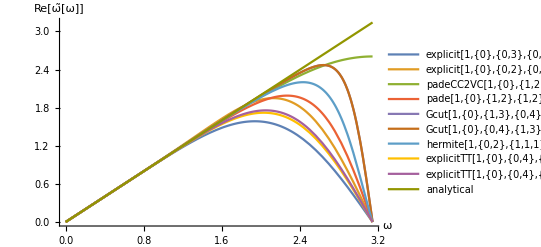

```mathematica
With[{fcns=Flatten@{Map[Re[ωassoc[#]]&,tags],η^dr}},
Plot[fcns,
{η,0,π},
PlotLegends->Flatten@{Map[#&,tags],"analytical"},
AxesLabel->{"ω","Re[ω̃[ω]]"},
PlotRange->All
]
]
```

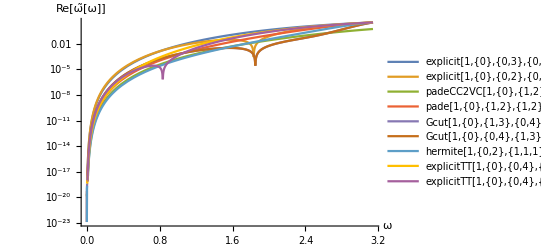

```mathematica
With[{fcns=Flatten@{Map[Abs[η^dr-Re[ωassoc[#]]]&,tags]}},
LogPlot[fcns,
{η,0,π},
PlotLegends->Flatten@Map[#&,tags],
AxesLabel->{"ω","Re[ω̃[ω]]"},
PlotRange->All
]
]
```

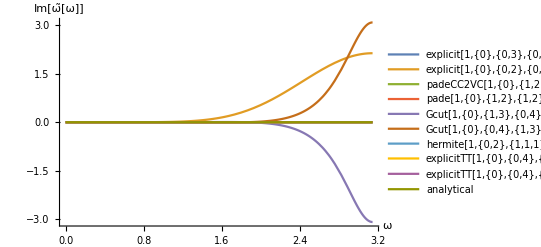

```mathematica
With[{fcns=Flatten@{Map[Im[ωassoc[#]]&,tags],0}},
Plot[fcns,
{η,0,π},
PlotLegends->Flatten@{Map[#&,tags],"analytical"},
AxesLabel->{"ω","Im[ω̃[ω]]"},
PlotRange->All
]
]
```

```mathematica
error=Table[
StringJoin["ω err: ",tags[[ix]]]==First@Normal@Tassoc[tags[[ix]]]
,{ix,1,Length[tags]}];
```

```mathematica
MatrixForm[error]
```

(ω err: explicit[1,{0},{0,3},{0,3},O(6)]==0.007143 η^6
ω err: explicit[1,{0},{0,2},{0,4},O(6)]==-0.009524 η^6
ω err: padeCC2VC[1,{0},{1,2},{1,2},O(6)]==0.0001702 η^6
ω err: pade[1,{0},{1,2},{1,2},O(6)]==0.0004762 η^6
ω err: Gcut[1,{0},{1,3},{0,4},O(6);2.00]==-0.001223 η^6
ω err: Gcut[1,{0},{0,4},{1,3},O(6);2.00]==-0.001223 η^6
ω err: hermite[1,{0,2},{1,1,1},{1,1,1},O(6)]==0.0001058 η^6
ω err: explicitTT[1,{0},{0,4},{0,4},O(6)|pade[1,{0},{1,2},{1,2},O(6)]]==0.0004762 η^6
ω err: explicitTT[1,{0},{0,4},{0,4},O(6)|Gcut[1,{0},{0,4},{1,3},O(6);2.00]]==-0.001223 η^6)

## [plots #2] Examine schemes (requires execution of all above sections)

```mathematica
MatrixForm[Keys[ωassoc]]
```

(explicit[1,{0},{0,3},{0,3},O(6)]
explicit[1,{0},{0,2},{0,4},O(6)]
pade[1,{0},{1,2},{1,2},O(6)]
pade[2,{0},{1,2},{1,2},O(6)]
pade[2,{0},{1,3},{1,3},O(8)]
pade[2,{0},{2,2},{2,2},O(8)]
pade[2,{0},{2,3},{2,3},O(10)]
pade[2,{0},{3,3},{3,3},O(12)]
hermite[2,{0,1},{0,2,2},{0,2,2},O(8)]
hermite[2,{0,1},{1,2,2},{1,2,2},O(10)]
hermite[1,{0,2},{1,1,1},{1,1,1},O(6)]
padeCC2VC[1,{0},{1,2},{1,2},O(6)]
Gexptaper[2,{0},{1,2},{1,2},O(4);{4.00,3.00}]
Gcut[1,{0},{0,4},{1,3},O(6);2.00]
Gcut[1,{0},{1,3},{0,4},O(6);2.00]
GcutTT[1,{0},{1,3},{0,4},O(6);2.00|TT[6:1e-6]]
GcutTT[1,{0,2},{0,4,0},{1,3,1},O(6);0.80|TT[6:1e-8]]
GcutTT[1,{0,2},{0,2,2},{1,2,2},O(6);2.40|TT[6:1e-8]|D[eta]_pi=0:0]
GcutTT[1,{0},{1,3},{0,3},O(6);2.20|TT[6:1e-8]]
explicitTT[1,{0},{0,4},{0,4},O(6)|Gcut[1,{0},{0,4},{1,3},O(6);2.00]]
explicitTT[1,{0},{0,4},{0,4},O(6)|pade[1,{0},{1,2},{1,2},O(6)]]
Gcut[2,{0},{0,4},{1,3},O(6);2.00]
Gcut[2,{0},{0,4},{1,3},O(6);0.25])

```mathematica
dr=2;
```

```mathematica
tags={
"pade[2,{0},{1,2},{1,2},O(6)]",
"Gcut[2,{0},{0,4},{1,3},O(6);0.25]",
"Gcut[2,{0},{0,4},{1,3},O(6);2.00]"
};
```

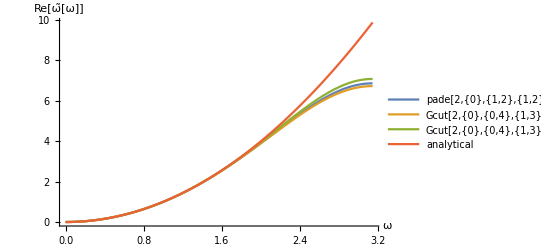

```mathematica
With[{fcns=Flatten@{Map[Re[ωassoc[#]]&,tags],η^dr}},
Plot[fcns,
{η,0,π},
PlotLegends->Flatten@{Map[#&,tags],"analytical"},
AxesLabel->{"ω","Re[ω̃[ω]]"},
PlotRange->All
]
]
```

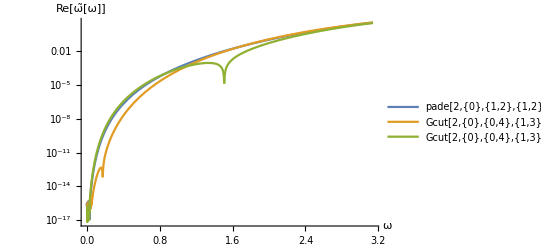

```mathematica
With[{fcns=Flatten@{Map[Abs[η^dr-Re[ωassoc[#]]]&,tags]}},
LogPlot[fcns,
{η,0,π},
PlotLegends->Flatten@Map[#&,tags],
AxesLabel->{"ω","Re[ω̃[ω]]"},
PlotRange->All
]
]
```

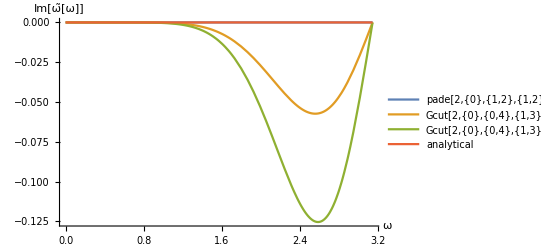

```mathematica
With[{fcns=Flatten@{Map[Im[ωassoc[#]]&,tags],0}},
Plot[fcns,
{η,0,π},
PlotLegends->Flatten@{Map[#&,tags],"analytical"},
AxesLabel->{"ω","Im[ω̃[ω]]"},
PlotRange->All
]
]
```

```mathematica
error=Table[
StringJoin["ω err: ",tags[[ix]]]==First@Normal@Tassoc[tags[[ix]]]
,{ix,1,Length[tags]}];
```

```mathematica
MatrixForm[error]
```

(ω err: pade[2,{0},{1,2},{1,2},O(6)]==0.0003042 η^6
ω err: Gcut[2,{0},{0,4},{1,3},O(6);0.25]==-6.682×10^-6 η^6
ω err: Gcut[2,{0},{0,4},{1,3},O(6);2.00]==-0.0005483 η^6)

## [plots #pap] Examine schemes (requires execution of all above sections)

```mathematica
Keys[ωassoc]
```

{explicit[1,{0},{0,3},{0,3},O(6)],explicit[1,{0},{0,2},{0,4},O(6)],pade[1,{0},{1,2},{1,2},O(6)],pade[2,{0},{1,2},{1,2},O(6)],pade[2,{0},{1,3},{1,3},O(8)],pade[2,{0},{2,2},{2,2},O(8)],pade[2,{0},{2,3},{2,3},O(10)],pade[2,{0},{3,3},{3,3},O(12)],hermite[2,{0,1},{0,2,2},{0,2,2},O(8)],hermite[2,{0,1},{1,2,2},{1,2,2},O(10)],hermite[1,{0,2},{1,1,1},{1,1,1},O(6)],padeCC2VC[1,{0},{1,2},{1,2},O(6)],Gexptaper[2,{0},{1,2},{1,2},O(4);{4.00,3.00}],Gcut[1,{0},{0,4},{1,3},O(6);2.00],Gcut[1,{0},{1,3},{0,4},O(6);2.00],GcutTT[1,{0},{1,3},{0,4},O(6);2.00|TT[6:1e-6]],GcutTT[1,{0,2},{0,4,0},{1,3,1},O(6);0.80|TT[6:1e-8]],GcutTT[1,{0,2},{0,2,2},{1,2,2},O(6);2.40|TT[6:1e-8]|D[eta]_pi=0:0],GcutTT[1,{0},{1,3},{0,3},O(6);2.20|TT[6:1e-8]],explicitTT[1,{0},{0,4},{0,4},O(6)|Gcut[1,{0},{0,4},{1,3},O(6);2.00]],explicitTT[1,{0},{0,4},{0,4},O(6)|pade[1,{0},{1,2},{1,2},O(6)]]}

```mathematica
dr=1;
```

```mathematica
tags={
"explicit[1,{0},{0,3},{0,3},O(6)]",
"explicit[1,{0},{0,4},{0,2},O(6)]",
"pade[1,{0},{1,2},{1,2},O(6)]",
"Gcut[1,{0},{1,3},{1,3},O(6);1.00]",
"Gcut[1,{0},{1,3},{0,4},O(6);1.00]",
"Gcut[1,{0},{0,2},{2,3},O(6);1.00]",
"padeCC2VC[1,{0},{1,2},{1,2},O(6)]",
"Hcut[1,{0,2},{1,3,2},{1,3,2},O(6);2.80]"
};
```

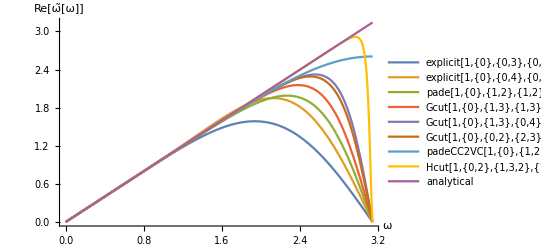

```mathematica
With[{fcns=Flatten@{Map[Re[ωassoc[#]]&,tags],η^dr}},
Plot[fcns,
{η,0,π},
PlotLegends->Flatten@{Map[#&,tags],"analytical"},
AxesLabel->{"ω","Re[ω̃[ω]]"},
PlotRange->All
]
]
```

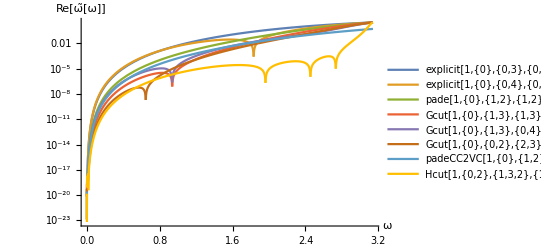

```mathematica
With[{fcns=Flatten@{Map[Abs[η^dr-Re[ωassoc[#]]]&,tags]}},
LogPlot[fcns,
{η,0,π},
PlotLegends->Flatten@Map[#&,tags],
AxesLabel->{"ω","Re[ω̃[ω]]"},
PlotRange->All
]
]
```

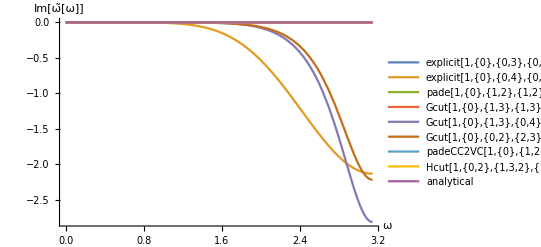

```mathematica
With[{fcns=Flatten@{Map[Im[ωassoc[#]]&,tags],0}},
Plot[fcns,
{η,0,π},
PlotLegends->Flatten@{Map[#&,tags],"analytical"},
AxesLabel->{"ω","Im[ω̃[ω]]"},
PlotRange->All
]
]
```

```mathematica
error=Table[
StringJoin["ω err: ",tags[[ix]]]==First@Normal@Tassoc[tags[[ix]]]
,{ix,1,Length[tags]}];
```

```mathematica
MatrixForm[error]
```

(ω err: explicit[1,{0},{0,3},{0,3},O(6)]==0.007143 η^6
ω err: explicit[1,{0},{0,4},{0,2},O(6)]==-0.009524 η^6
ω err: pade[1,{0},{1,2},{1,2},O(6)]==0.0004762 η^6
ω err: Gcut[1,{0},{1,3},{1,3},O(6);1.00]==-0.00005281 η^6
ω err: Gcut[1,{0},{1,3},{0,4},O(6);1.00]==-0.000237 η^6
ω err: Gcut[1,{0},{0,2},{2,3},O(6);1.00]==-0.00001325 η^6
ω err: padeCC2VC[1,{0},{1,2},{1,2},O(6)]==0.0001702 η^6
ω err: Hcut[1,{0,2},{1,3,2},{1,3,2},O(6);2.80]==-4.924×10^-6 η^6)

## [paper-plots] Dump a selection of functions sampled for plotting

```mathematica
(*dump to CSV for plotting with matplotlib script*)
```

```mathematica
ωdumptag={
{"explicit[1,{0},{0,3},{0,3},O(6)]",
"explicit_d1_0_03_03_O6"},
{"explicit[1,{0},{0,4},{0,2},O(6)]",
"explicit_d1_0_04_02_O6"},
{"pade[1,{0},{1,2},{1,2},O(6)]",
"pade_d1_0_12_12_O6"},
{"Gcut[1,{0},{1,3},{1,3},O(6);1.00]",
"gcut_d1_0_13_13_O6_1.00"},
{"Gcut[1,{0},{1,3},{0,4},O(6);1.00]",
"gcut_d1_0_13_04_O6_1.00"},
{"Gcut[1,{0},{0,2},{2,3},O(6);1.00]",
"gcut_d1_0_02_23_O6_1.00"},
{"padeCC2VC[1,{0},{1,2},{1,2},O(6)]",
"padecc2vc_d1_0_12_12_O6"},
{"Hcut[1,{0,2},{1,3,2},{1,3,2},O(6);2.80]",
"hcut_d1_02_132_132_O6_2.80"}
};
```

```mathematica
ηdp=30;
Nηtot=1024;
ηa=0;
ηb=π;
ηran[Nη_]:=Table[(ηb-ηa)/(Nη-1)i,{i,0,Nη-1}];
```

```mathematica
Block[{ωtmp,ωdumptup,ix},
For[ix=1,ix≤Length[ωdumptag],ix++,

With[{ηsamp=N[ηran[Nηtot],ηdp],
ωtag=ωdumptag[[ix]][[1]],
ωdumpfn=ωdumptag[[ix]][[2]]},

ωtmp=ωassoc[ωtag]/.η->ηsamp;

ωdumptup={ηsamp,Re[ωtmp],Im[ωtmp]};

Export[
StringJoin[NotebookDirectory[],ωdumpfn],
Transpose[ωdumptup],
"CSV"];
]
]
]
```

## [paper-example] Taylor constraints construction

```mathematica
(*Taylor constraints: wlog δx=1*)
dr=1;
ds={0,2};
mL={0,1,0};
mR={1,2,0};
(*one term (scaling) is fixed so -1*)
p=Total@Flatten[Table[Table[1,{i,-mL[[ixc]],mR[[ixc]]}],{ixc,1,Length[mL]}]]-1;
```

```mathematica
p=Total[mL]+Total[mR]+Length[mL]-1;
```

```mathematica
3mAB2width[mL,mR]+Length[mL]
```

9

```mathematica
tCons=TEqnsTerms[dr,ds,mAB2width[mL,mR],p]/.δx->1;
zCons=mZeroConstraints[dr,ds,mL,mR];
```

```mathematica
(*fix overall scaling for b[d,0]*)
eqs=Flatten@{
tCons[[1;;p]]/.Flatten@Map[ToRules,zCons],
bv[dr,0]==1
};
```

```mathematica
vars=mSolveVars[dr,ds,mL,mR];
```

```mathematica
{p,Length@vars,Length@tCons[[1;;p]],Length@eqs}
```

{6,7,6,7}

```mathematica
Simplify[
tCons[[1;;p]]/.Flatten@Map[ToRules,zCons]
]
```

{av[0,-1]+av[0,0]+av[0,1]+av[0,2]==0,av[0,-1]+bv[1,0]+bv[1,1]==av[0,1]+2 av[0,2],av[0,-1]+av[0,1]+4 av[0,2]+2 av[2,0]==2 bv[1,1],av[0,-1]+3 bv[1,1]==av[0,1]+8 av[0,2],av[0,-1]+av[0,1]+16 av[0,2]==4 bv[1,1],av[0,-1]+5 bv[1,1]==av[0,1]+32 av[0,2]}

```mathematica
vars
```

{av[0,-1],av[0,0],av[0,1],av[0,2],av[2,0],bv[1,0],bv[1,1]}

```mathematica
sols=GFDSolver[eqs,vars];
```

```mathematica
rsols=Rationalize[sols,10^(-20)]
```

{av[0,-1]→1/9,av[0,0]→-11/6,av[0,1]→5/3,av[0,2]→1/18,av[2,0]→-1/3,bv[1,0]→1,bv[1,1]→2/3}

```mathematica
sols
```

{av[0,-1]→0.1111111111111111111111111111111111111111111111111111111111,av[0,0]→-1.833333333333333333333333333333333333333333333333333333333,av[0,1]→1.666666666666666666666666666666666666666666666666666666667,av[0,2]→0.05555555555555555555555555555555555555555555555555555555556,av[2,0]→-0.3333333333333333333333333333333333333333333333333333333333,bv[1,0]→1.,bv[1,1]→0.6666666666666666666666666666666666666666666666666666666667}

```mathematica
tag="tmp";
```

```mathematica
Sassoc[tag]=ExportStencil[sols,dr,ds,mL,mR,PG];
```

```mathematica
TaylorRescaleRat["tmp",1,ds,mL,mR,10]
```

1/900 δx^5 u^(6)[x]+(δx^6 u^(7)[x])/2100+(δx^7 u^(8)[x])/6300+(δx^8 u^(9)[x])/25200+(13 δx^9 u^(10)[x])/1512000

```mathematica
(* verify Taylor / zero constaints satisfied *)
tCons/.Flatten@Map[ToRules,zCons]/.Rationalize[sols,10^(-20)]
```

{True,True,True,True,True,True}